# Optimizing QSAR with DFT Variables

#### A validation of the Results from Aouidate, et al. “Combining DFT and QSAR studies for predicting psychotomimeticactivity of substituted phenethylamines using statistical methods.” Journal of Taibah University for Science 10 (2016): 787-96.

## Background

The medicinal value of drugs is optimized via Quantitative Structure-Activity Relationships, or QSAR. QSAR seeks to explain the variation in the biological activity of related molecules via variations in their structure and physicochemical properties. Synthesizing and testing new compounds is time-consuming and expensive, so the faster we can reach a mathematical model with predictive power, the better. The physicochemical properties of compounds used in such studies are ultimately a function of the compounds’ electronic structure. The electronic structure of molecules can be computed using Density Functional Theory, or DFT. This is a computationally intensive process, but newer software is becoming more efficient and accessible. Aouidate, et al collected from the literature the biochemical activities of 46 phenalkylamines, a frequently-abused class of psychoactive drugs. They calculated the DFT parameters Etotal, Ehomo, Elumo, dipole moment (DM), and absolute hardness (η), and physicochemical properties such as molecular weight, density, and octanol/water partition coefficient (logP). For phenalkylamines, biological activity is expressed in Mescaline Units (logMU).
	The original paper used a set of physicochemical descriptors that largely corresponded to macroscale properties and struck me as not biologically relevant. I have generated a more balanced data set with more traditional pharmacological descriptors, which I will test below.

## Code

### Importing Data

```mathematica
newdata1=Import["/Users/themarchhare/Documents/GitHub/Project/Molecular Structures Real/Descriptors 2.xlsx"];
```

```mathematica
FirstSheet1=Part[newdata1,1] ;
```

```mathematica
FirstNewData=Part[FirstSheet1,2;;-18,1;;-3]
```

(−82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 0.046 | −0.707 | 274.154 | 37.9 | 1.324 | 2.04 | -2.94 | 44.48 | -2.1 | 2.8154 | 2.72
−30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 0.135 | −0.708 | 255.376 | 42.6 | 1.08 | 2.29 | -3.18 | 69.78 | 0.19 | 2.2187 | 1.96
−19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 0.126 | −0.712 | 223.311 | 33.9 | 0.998 | 2.07 | -2.61 | 44.48 | -0.47 | 2.4151 | 2.02
−20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 0.126 | −0.709 | 237.338 | 33.9 | 0.998 | 2.53 | -2.88 | 44.48 | -2.43 | 2.4073 | 1.95
−18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 0.127 | −0.710 | 209.285 | 34.2 | 1.01 | 1.66 | -2.45 | 44.48 | -0.31 | 2.3756 | 1.9
−31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | −0.150 | −0.712 | 269.403 | 41.2 | 1.07 | 2.69 | -3.38 | 69.78 | 0.86 | 3.9221 | 1.71
−86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 0.046 | −0.709 | 260.128 | 39.5 | 1.368 | 1.68 | -2.56 | 44.48 | -2.71 | 2.7816 | 1.69
−21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 0.122 | −0.713 | 251.365 | 33.9 | 0.979 | 2.98 | -3.14 | 44.48 | -5.7 | 2.2935 | 1.68
−29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | −0.131 | −0.707 | 241.35 | 43.1 | 1.1 | 1.79 | -2.95 | 69.78 | 0.01 | 3.8763 | 1.66
−29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | −0.219 | −0.713 | 241.35 | 44.2 | 1.1 | 1.93 | -2.8 | 69.78 | 1.48 | 3.5554 | 1.36
−20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 0.349 | −0.713 | 225.284 | 34.3 | 1.048 | 1.24 | -2.12 | 53.71 | 0.68 | 3.7961 | 1.33
−18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 0.125 | −0.716 | 209.285 | 34.9 | 1.012 | 1.71 | -2.23 | 44.48 | -1.08 | 1.3017 | 1.25
−30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | −0.220 | −0.707 | 255.376 | 43.6 | 1.09 | 2.38 | -3.07 | 69.78 | 1.43 | 3.5394 | 1.29
−17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 0.133 | −0.714 | 195.258 | 35.3 | 1.026 | 1.3 | -2.07 | 44.48 | -0.92 | 1.2589 | 1.27
−22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 0.273 | −0.713 | 239.268 | 43.5 | 1.184 | 1.43 | -2.81 | 62.94 | -1.15 | 1.3148 | 1.14
−21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 0.353 | −0.707 | 239.311 | 34.3 | 1.034 | 1.65 | -2.42 | 53.71 | -1.63 | 3.5769 | 1.36
−28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | −0.223 | −0.708 | 227.323 | 45. | 1.12 | 1.43 | -2.57 | 69.78 | 1.33 | 3.5557 | 1.11
−19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 0.326 | −0.707 | 209.242 | 45.4 | 1.175 | 1.5 | -2.8 | 53.71 | -0.45 | 2.5885 | 1.
−21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 0.265 | −0.713 | 239.311 | 34.3 | 1.034 | 1.65 | -2.42 | 53.71 | 0.43 | 2.9286 | 1.05
−19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 0.326 | −0.715 | 209.242 | 45.4 | 1.175 | 1.5 | -2.79 | 53.71 | -0.56 | 2.065 | 1.
−22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 0.352 | −0.713 | 253.337 | 34.2 | 1.022 | 2.1 | -2.69 | 53.71 | -0.53 | 3.6099 | 1.38
−20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 0.225 | −0.714 | 225.284 | 35.2 | 1.05 | 1.29 | -2.04 | 53.71 | -0.04 | 2.9414 | 0.87
−23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 0.269 | −0.714 | 255.31 | 34. | 1.069 | 1.17 | -2.14 | 62.94 | -1.21 | 5.1462 | 0.86
−21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 0.264 | −0.714 | 239.311 | 35.1 | 1.036 | 1.75 | -2.31 | 53.71 | 1.01 | 4.9241 | 0.83
−29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 0.293 | −0.712 | 241.35 | 44.2 | 1.1 | 1.93 | -2.8 | 69.78 | 2.35 | 5.1501 | 0.84
−29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 0.289 | −0.708 | 241.35 | 44.2 | 1.1 | 1.84 | -2.87 | 69.78 | -0.78 | 5.1634 | 0.84
−28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 0.293 | −0.702 | 227.323 | 45. | 1.12 | 1.43 | -2.57 | 69.78 | 2.21 | 5.1512 | 0.81
−22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.283 | −0.702 | 239.268 | 43.5 | 1.184 | 1.43 | -2.81 | 62.94 | -1.15 | 0.8071 | 0.76
−29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | −0.226 | −0.705 | 241.35 | 44.2 | 1.1 | 1.84 | -2.87 | 69.78 | -1.06 | 3.5591 | 0.66
−30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | −0.222 | −0.713 | 255.376 | 43.6 | 1.09 | 2.34 | -3.1 | 69.78 | -0.88 | 3.5628 | 0.68
−17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 0.378 | −0.713 | 195.258 | 34.7 | 1.023 | 1.31 | -2.1 | 44.48 | -2. | 2.87 | 0.67
−12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 0.179 | −0.707 | 149.233 | 35.2 | 0.938 | 1.8 | -2.41 | 26.02 | -1.75 | 1.3362 | 0.59
−31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | −0.219 | −0.712 | 269.403 | 43.1 | 1.07 | 2.84 | -3.34 | 69.78 | -0.69 | 5.2338 | 0.58
−26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 0.267 | −0.712 | 301.38 | 39.8 | 1.093 | 2.66 | -3.44 | 53.71 | -3.54 | 4.8593 | 0.46
−19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 0.265 | −0.713 | 209.242 | 45.4 | 1.175 | 1.5 | -2.79 | 53.71 | 0.81 | 2.8125 | 0.43
−16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 0.329 | −0.708 | 179.216 | 48. | 1.163 | 1.57 | -2.78 | 44.48 | 0.11 | 1.3784 | 0.41
−22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 0.265 | −0.713 | 253.337 | 35. | 1.023 | 2.2 | -2.58 | 53.71 | -3.79 | 4.914 | 0.38
−30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 0.3 | −0.711 | 255.376 | 43.6 | 1.09 | 2.34 | -3.1 | 69.78 | -0.6 | 5.1602 | 0.38
−30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 0.285 | −0.710 | 255.376 | 43.6 | 1.09 | 2.24 | -3.17 | 69.78 | -2.06 | 5.1389 | 0.38
−20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 0.245 | −0.719 | 225.284 | 34.3 | 1.048 | 1.24 | -2.12 | 53.71 | 3.93 | 4.5648 | 0.33
−21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 0.26 | −0.713 | 239.311 | 35.1 | 1.036 | 1.7 | -2.34 | 53.71 | -1.07 | 2.8654 | 0.23
−20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 0.249 | −0.713 | 225.284 | 35.2 | 1.05 | 1.29 | -2.04 | 53.71 | 0.59 | 2.8561 | 0.03
−19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 0.253 | −0.707 | 211.258 | 35.4 | 1.067 | 0.88 | -1.74 | 53.71 | 3.64 | 2.9357 | 0.
−19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 0.305 | −0.710 | 211.258 | 35.4 | 1.067 | 0.88 | -1.74 | 53.71 | 0.01 | 2.8568 | −0.030
−17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 0.308 | −0.717 | 195.258 | 34.7 | 1.023 | 1.31 | -2.1 | 44.48 | 2.81 | 3.5818 | −0.060
−16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 0.307 | −0.713 | 181.232 | 36. | 1.041 | 0.95 | -1.72 | 44.48 | 2.43 | 3.3747 | −0.670)

```mathematica
(*List of descriptors in order*)
```

```mathematica
FirstSheet1[[1]]
```

{ET,IP,EHOMO,η,ELUMO,Qp,Qmin,MW,γ,D,cLogP,Solubility,TPSA,Druglikeness,Dipole moment from Millsian,logMU,,DFT}

```mathematica
DatatoUse=ReplaceAll[FirstNewData,s_String:>ToExpression[s]]
```

(-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 0.046 | -0.707 | 274.154 | 37.9 | 1.324 | 2.04 | -2.94 | 44.48 | -2.1 | 2.8154 | 2.72
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 0.135 | -0.708 | 255.376 | 42.6 | 1.08 | 2.29 | -3.18 | 69.78 | 0.19 | 2.2187 | 1.96
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 0.126 | -0.712 | 223.311 | 33.9 | 0.998 | 2.07 | -2.61 | 44.48 | -0.47 | 2.4151 | 2.02
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 0.126 | -0.709 | 237.338 | 33.9 | 0.998 | 2.53 | -2.88 | 44.48 | -2.43 | 2.4073 | 1.95
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 0.127 | -0.71 | 209.285 | 34.2 | 1.01 | 1.66 | -2.45 | 44.48 | -0.31 | 2.3756 | 1.9
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | -0.15 | -0.712 | 269.403 | 41.2 | 1.07 | 2.69 | -3.38 | 69.78 | 0.86 | 3.9221 | 1.71
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 0.046 | -0.709 | 260.128 | 39.5 | 1.368 | 1.68 | -2.56 | 44.48 | -2.71 | 2.7816 | 1.69
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 0.122 | -0.713 | 251.365 | 33.9 | 0.979 | 2.98 | -3.14 | 44.48 | -5.7 | 2.2935 | 1.68
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | -0.131 | -0.707 | 241.35 | 43.1 | 1.1 | 1.79 | -2.95 | 69.78 | 0.01 | 3.8763 | 1.66
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | -0.219 | -0.713 | 241.35 | 44.2 | 1.1 | 1.93 | -2.8 | 69.78 | 1.48 | 3.5554 | 1.36
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 0.349 | -0.713 | 225.284 | 34.3 | 1.048 | 1.24 | -2.12 | 53.71 | 0.68 | 3.7961 | 1.33
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 0.125 | -0.716 | 209.285 | 34.9 | 1.012 | 1.71 | -2.23 | 44.48 | -1.08 | 1.3017 | 1.25
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | -0.22 | -0.707 | 255.376 | 43.6 | 1.09 | 2.38 | -3.07 | 69.78 | 1.43 | 3.5394 | 1.29
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 0.133 | -0.714 | 195.258 | 35.3 | 1.026 | 1.3 | -2.07 | 44.48 | -0.92 | 1.2589 | 1.27
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 0.273 | -0.713 | 239.268 | 43.5 | 1.184 | 1.43 | -2.81 | 62.94 | -1.15 | 1.3148 | 1.14
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 0.353 | -0.707 | 239.311 | 34.3 | 1.034 | 1.65 | -2.42 | 53.71 | -1.63 | 3.5769 | 1.36
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | -0.223 | -0.708 | 227.323 | 45. | 1.12 | 1.43 | -2.57 | 69.78 | 1.33 | 3.5557 | 1.11
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 0.326 | -0.707 | 209.242 | 45.4 | 1.175 | 1.5 | -2.8 | 53.71 | -0.45 | 2.5885 | 1.
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 0.265 | -0.713 | 239.311 | 34.3 | 1.034 | 1.65 | -2.42 | 53.71 | 0.43 | 2.9286 | 1.05
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 0.326 | -0.715 | 209.242 | 45.4 | 1.175 | 1.5 | -2.79 | 53.71 | -0.56 | 2.065 | 1.
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 0.352 | -0.713 | 253.337 | 34.2 | 1.022 | 2.1 | -2.69 | 53.71 | -0.53 | 3.6099 | 1.38
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 0.225 | -0.714 | 225.284 | 35.2 | 1.05 | 1.29 | -2.04 | 53.71 | -0.04 | 2.9414 | 0.87
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 0.269 | -0.714 | 255.31 | 34. | 1.069 | 1.17 | -2.14 | 62.94 | -1.21 | 5.1462 | 0.86
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 0.264 | -0.714 | 239.311 | 35.1 | 1.036 | 1.75 | -2.31 | 53.71 | 1.01 | 4.9241 | 0.83
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 0.293 | -0.712 | 241.35 | 44.2 | 1.1 | 1.93 | -2.8 | 69.78 | 2.35 | 5.1501 | 0.84
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 0.289 | -0.708 | 241.35 | 44.2 | 1.1 | 1.84 | -2.87 | 69.78 | -0.78 | 5.1634 | 0.84
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 0.293 | -0.702 | 227.323 | 45. | 1.12 | 1.43 | -2.57 | 69.78 | 2.21 | 5.1512 | 0.81
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.283 | -0.702 | 239.268 | 43.5 | 1.184 | 1.43 | -2.81 | 62.94 | -1.15 | 0.8071 | 0.76
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | -0.226 | -0.705 | 241.35 | 44.2 | 1.1 | 1.84 | -2.87 | 69.78 | -1.06 | 3.5591 | 0.66
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | -0.222 | -0.713 | 255.376 | 43.6 | 1.09 | 2.34 | -3.1 | 69.78 | -0.88 | 3.5628 | 0.68
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 0.378 | -0.713 | 195.258 | 34.7 | 1.023 | 1.31 | -2.1 | 44.48 | -2. | 2.87 | 0.67
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 0.179 | -0.707 | 149.233 | 35.2 | 0.938 | 1.8 | -2.41 | 26.02 | -1.75 | 1.3362 | 0.59
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | -0.219 | -0.712 | 269.403 | 43.1 | 1.07 | 2.84 | -3.34 | 69.78 | -0.69 | 5.2338 | 0.58
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 0.267 | -0.712 | 301.38 | 39.8 | 1.093 | 2.66 | -3.44 | 53.71 | -3.54 | 4.8593 | 0.46
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 0.265 | -0.713 | 209.242 | 45.4 | 1.175 | 1.5 | -2.79 | 53.71 | 0.81 | 2.8125 | 0.43
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 0.329 | -0.708 | 179.216 | 48. | 1.163 | 1.57 | -2.78 | 44.48 | 0.11 | 1.3784 | 0.41
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 0.265 | -0.713 | 253.337 | 35. | 1.023 | 2.2 | -2.58 | 53.71 | -3.79 | 4.914 | 0.38
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 0.3 | -0.711 | 255.376 | 43.6 | 1.09 | 2.34 | -3.1 | 69.78 | -0.6 | 5.1602 | 0.38
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 0.285 | -0.71 | 255.376 | 43.6 | 1.09 | 2.24 | -3.17 | 69.78 | -2.06 | 5.1389 | 0.38
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 0.245 | -0.719 | 225.284 | 34.3 | 1.048 | 1.24 | -2.12 | 53.71 | 3.93 | 4.5648 | 0.33
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 0.26 | -0.713 | 239.311 | 35.1 | 1.036 | 1.7 | -2.34 | 53.71 | -1.07 | 2.8654 | 0.23
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 0.249 | -0.713 | 225.284 | 35.2 | 1.05 | 1.29 | -2.04 | 53.71 | 0.59 | 2.8561 | 0.03
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 0.253 | -0.707 | 211.258 | 35.4 | 1.067 | 0.88 | -1.74 | 53.71 | 3.64 | 2.9357 | 0.
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 0.305 | -0.71 | 211.258 | 35.4 | 1.067 | 0.88 | -1.74 | 53.71 | 0.01 | 2.8568 | -0.03
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 0.308 | -0.717 | 195.258 | 34.7 | 1.023 | 1.31 | -2.1 | 44.48 | 2.81 | 3.5818 | -0.06
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 0.307 | -0.713 | 181.232 | 36. | 1.041 | 0.95 | -1.72 | 44.48 | 2.43 | 3.3747 | -0.67)

```mathematica
Dimensions[DatatoUse]
```

{46,16}

### Normalization

```mathematica
transpose=Transpose[DatatoUse]
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.04 | 2.29 | 2.07 | 2.53 | 1.66 | 2.69 | 1.68 | 2.98 | 1.79 | 1.93 | 1.24 | 1.71 | 2.38 | 1.3 | 1.43 | 1.65 | 1.43 | 1.5 | 1.65 | 1.5 | 2.1 | 1.29 | 1.17 | 1.75 | 1.93 | 1.84 | 1.43 | 1.43 | 1.84 | 2.34 | 1.31 | 1.8 | 2.84 | 2.66 | 1.5 | 1.57 | 2.2 | 2.34 | 2.24 | 1.24 | 1.7 | 1.29 | 0.88 | 0.88 | 1.31 | 0.95
-2.94 | -3.18 | -2.61 | -2.88 | -2.45 | -3.38 | -2.56 | -3.14 | -2.95 | -2.8 | -2.12 | -2.23 | -3.07 | -2.07 | -2.81 | -2.42 | -2.57 | -2.8 | -2.42 | -2.79 | -2.69 | -2.04 | -2.14 | -2.31 | -2.8 | -2.87 | -2.57 | -2.81 | -2.87 | -3.1 | -2.1 | -2.41 | -3.34 | -3.44 | -2.79 | -2.78 | -2.58 | -3.1 | -3.17 | -2.12 | -2.34 | -2.04 | -1.74 | -1.74 | -2.1 | -1.72
44.48 | 69.78 | 44.48 | 44.48 | 44.48 | 69.78 | 44.48 | 44.48 | 69.78 | 69.78 | 53.71 | 44.48 | 69.78 | 44.48 | 62.94 | 53.71 | 69.78 | 53.71 | 53.71 | 53.71 | 53.71 | 53.71 | 62.94 | 53.71 | 69.78 | 69.78 | 69.78 | 62.94 | 69.78 | 69.78 | 44.48 | 26.02 | 69.78 | 53.71 | 53.71 | 44.48 | 53.71 | 69.78 | 69.78 | 53.71 | 53.71 | 53.71 | 53.71 | 53.71 | 44.48 | 44.48
-2.1 | 0.19 | -0.47 | -2.43 | -0.31 | 0.86 | -2.71 | -5.7 | 0.01 | 1.48 | 0.68 | -1.08 | 1.43 | -0.92 | -1.15 | -1.63 | 1.33 | -0.45 | 0.43 | -0.56 | -0.53 | -0.04 | -1.21 | 1.01 | 2.35 | -0.78 | 2.21 | -1.15 | -1.06 | -0.88 | -2. | -1.75 | -0.69 | -3.54 | 0.81 | 0.11 | -3.79 | -0.6 | -2.06 | 3.93 | -1.07 | 0.59 | 3.64 | 0.01 | 2.81 | 2.43
2.8154 | 2.2187 | 2.4151 | 2.4073 | 2.3756 | 3.9221 | 2.7816 | 2.2935 | 3.8763 | 3.5554 | 3.7961 | 1.3017 | 3.5394 | 1.2589 | 1.3148 | 3.5769 | 3.5557 | 2.5885 | 2.9286 | 2.065 | 3.6099 | 2.9414 | 5.1462 | 4.9241 | 5.1501 | 5.1634 | 5.1512 | 0.8071 | 3.5591 | 3.5628 | 2.87 | 1.3362 | 5.2338 | 4.8593 | 2.8125 | 1.3784 | 4.914 | 5.1602 | 5.1389 | 4.5648 | 2.8654 | 2.8561 | 2.9357 | 2.8568 | 3.5818 | 3.3747
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
Dimensions[transpose]
```

{16,46}

```mathematica
ToNormalize=transpose[[1;;-2]]
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.04 | 2.29 | 2.07 | 2.53 | 1.66 | 2.69 | 1.68 | 2.98 | 1.79 | 1.93 | 1.24 | 1.71 | 2.38 | 1.3 | 1.43 | 1.65 | 1.43 | 1.5 | 1.65 | 1.5 | 2.1 | 1.29 | 1.17 | 1.75 | 1.93 | 1.84 | 1.43 | 1.43 | 1.84 | 2.34 | 1.31 | 1.8 | 2.84 | 2.66 | 1.5 | 1.57 | 2.2 | 2.34 | 2.24 | 1.24 | 1.7 | 1.29 | 0.88 | 0.88 | 1.31 | 0.95
-2.94 | -3.18 | -2.61 | -2.88 | -2.45 | -3.38 | -2.56 | -3.14 | -2.95 | -2.8 | -2.12 | -2.23 | -3.07 | -2.07 | -2.81 | -2.42 | -2.57 | -2.8 | -2.42 | -2.79 | -2.69 | -2.04 | -2.14 | -2.31 | -2.8 | -2.87 | -2.57 | -2.81 | -2.87 | -3.1 | -2.1 | -2.41 | -3.34 | -3.44 | -2.79 | -2.78 | -2.58 | -3.1 | -3.17 | -2.12 | -2.34 | -2.04 | -1.74 | -1.74 | -2.1 | -1.72
44.48 | 69.78 | 44.48 | 44.48 | 44.48 | 69.78 | 44.48 | 44.48 | 69.78 | 69.78 | 53.71 | 44.48 | 69.78 | 44.48 | 62.94 | 53.71 | 69.78 | 53.71 | 53.71 | 53.71 | 53.71 | 53.71 | 62.94 | 53.71 | 69.78 | 69.78 | 69.78 | 62.94 | 69.78 | 69.78 | 44.48 | 26.02 | 69.78 | 53.71 | 53.71 | 44.48 | 53.71 | 69.78 | 69.78 | 53.71 | 53.71 | 53.71 | 53.71 | 53.71 | 44.48 | 44.48
-2.1 | 0.19 | -0.47 | -2.43 | -0.31 | 0.86 | -2.71 | -5.7 | 0.01 | 1.48 | 0.68 | -1.08 | 1.43 | -0.92 | -1.15 | -1.63 | 1.33 | -0.45 | 0.43 | -0.56 | -0.53 | -0.04 | -1.21 | 1.01 | 2.35 | -0.78 | 2.21 | -1.15 | -1.06 | -0.88 | -2. | -1.75 | -0.69 | -3.54 | 0.81 | 0.11 | -3.79 | -0.6 | -2.06 | 3.93 | -1.07 | 0.59 | 3.64 | 0.01 | 2.81 | 2.43
2.8154 | 2.2187 | 2.4151 | 2.4073 | 2.3756 | 3.9221 | 2.7816 | 2.2935 | 3.8763 | 3.5554 | 3.7961 | 1.3017 | 3.5394 | 1.2589 | 1.3148 | 3.5769 | 3.5557 | 2.5885 | 2.9286 | 2.065 | 3.6099 | 2.9414 | 5.1462 | 4.9241 | 5.1501 | 5.1634 | 5.1512 | 0.8071 | 3.5591 | 3.5628 | 2.87 | 1.3362 | 5.2338 | 4.8593 | 2.8125 | 1.3784 | 4.914 | 5.1602 | 5.1389 | 4.5648 | 2.8654 | 2.8561 | 2.9357 | 2.8568 | 3.5818 | 3.3747)

```mathematica
Dimensions[ToNormalize]
```

{15,46}

```mathematica
Clear[g]
```

```mathematica
g[list_]:=list/list[[43]]
```

```mathematica
g[ToNormalize[[1]]]
```

{4.26288,1.56584,1.00484,1.06023,0.949452,1.62123,4.46109,1.11562,1.51045,1.51044,1.0554,0.949447,1.56584,0.894055,1.15966,1.11079,1.45506,0.998319,1.11079,0.998323,1.16618,1.0554,1.21673,1.11078,1.51044,1.51044,1.45506,1.15966,1.51044,1.56584,0.894061,0.626755,1.62122,1.38093,0.998319,0.836977,1.16617,1.56584,1.56584,1.0554,1.11079,1.05539,1.,0.999993,0.894052,0.838658}

```mathematica
RatioNormalized=Map[g,ToNormalize]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1. | 1.00141 | 1.00707 | 1.00283 | 1.00424 | 1.00707 | 1.00283 | 1.00849 | 1. | 1.00849 | 1.00849 | 1.01273 | 1. | 1.0099 | 1.00849 | 1. | 1.00141 | 1. | 1.00849 | 1.01132 | 1.00849 | 1.0099 | 1.0099 | 1.0099 | 1.00707 | 1.00141 | 0.992928 | 0.992928 | 0.997171 | 1.00849 | 1.00849 | 1. | 1.00707 | 1.00707 | 1.00849 | 1.00141 | 1.00849 | 1.00566 | 1.00424 | 1.01697 | 1.00849 | 1.00849 | 1. | 1.00424 | 1.01414 | 1.00849
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
2.31818 | 2.60227 | 2.35227 | 2.875 | 1.88636 | 3.05682 | 1.90909 | 3.38636 | 2.03409 | 2.19318 | 1.40909 | 1.94318 | 2.70455 | 1.47727 | 1.625 | 1.875 | 1.625 | 1.70455 | 1.875 | 1.70455 | 2.38636 | 1.46591 | 1.32955 | 1.98864 | 2.19318 | 2.09091 | 1.625 | 1.625 | 2.09091 | 2.65909 | 1.48864 | 2.04545 | 3.22727 | 3.02273 | 1.70455 | 1.78409 | 2.5 | 2.65909 | 2.54545 | 1.40909 | 1.93182 | 1.46591 | 1. | 1. | 1.48864 | 1.07955
1.68966 | 1.82759 | 1.5 | 1.65517 | 1.40805 | 1.94253 | 1.47126 | 1.8046 | 1.6954 | 1.6092 | 1.21839 | 1.28161 | 1.76437 | 1.18966 | 1.61494 | 1.3908 | 1.47701 | 1.6092 | 1.3908 | 1.60345 | 1.54598 | 1.17241 | 1.22989 | 1.32759 | 1.6092 | 1.64943 | 1.47701 | 1.61494 | 1.64943 | 1.78161 | 1.2069 | 1.38506 | 1.91954 | 1.97701 | 1.60345 | 1.5977 | 1.48276 | 1.78161 | 1.82184 | 1.21839 | 1.34483 | 1.17241 | 1. | 1. | 1.2069 | 0.988506
0.828151 | 1.2992 | 0.828151 | 0.828151 | 0.828151 | 1.2992 | 0.828151 | 0.828151 | 1.2992 | 1.2992 | 1. | 0.828151 | 1.2992 | 0.828151 | 1.17185 | 1. | 1.2992 | 1. | 1. | 1. | 1. | 1. | 1.17185 | 1. | 1.2992 | 1.2992 | 1.2992 | 1.17185 | 1.2992 | 1.2992 | 0.828151 | 0.484454 | 1.2992 | 1. | 1. | 0.828151 | 1. | 1.2992 | 1.2992 | 1. | 1. | 1. | 1. | 1. | 0.828151 | 0.828151
-0.576923 | 0.0521978 | -0.129121 | -0.667582 | -0.0851648 | 0.236264 | -0.744505 | -1.56593 | 0.00274725 | 0.406593 | 0.186813 | -0.296703 | 0.392857 | -0.252747 | -0.315934 | -0.447802 | 0.365385 | -0.123626 | 0.118132 | -0.153846 | -0.145604 | -0.010989 | -0.332418 | 0.277473 | 0.645604 | -0.214286 | 0.607143 | -0.315934 | -0.291209 | -0.241758 | -0.549451 | -0.480769 | -0.18956 | -0.972527 | 0.222527 | 0.0302198 | -1.04121 | -0.164835 | -0.565934 | 1.07967 | -0.293956 | 0.162088 | 1. | 0.00274725 | 0.771978 | 0.667582
0.959022 | 0.755765 | 0.822666 | 0.820009 | 0.809211 | 1.336 | 0.947508 | 0.781245 | 1.3204 | 1.21109 | 1.29308 | 0.443404 | 1.20564 | 0.428824 | 0.447866 | 1.21841 | 1.21119 | 0.881732 | 0.997581 | 0.70341 | 1.22966 | 1.00194 | 1.75297 | 1.67732 | 1.7543 | 1.75883 | 1.75468 | 0.274926 | 1.21235 | 1.21361 | 0.97762 | 0.455155 | 1.78281 | 1.65524 | 0.958034 | 0.46953 | 1.67388 | 1.75774 | 1.75049 | 1.55493 | 0.976053 | 0.972886 | 1. | 0.973124 | 1.22008 | 1.14954)

```mathematica
Dimensions[RatioNormalized]
```

{15,46}

```mathematica
RatioNormalizedT=Transpose[RatioNormalized]
```

(4.26288 | 1.00751 | 1.02879 | 0.933717 | -0.409207 | 0.181818 | 1. | 1.29772 | 1.07062 | 1.24086 | 2.31818 | 1.68966 | 0.828151 | -0.576923 | 0.959022
1.56584 | 0.973494 | 0.982799 | 0.889077 | -0.434783 | 0.533597 | 1.00141 | 1.20883 | 1.20339 | 1.01218 | 2.60227 | 1.82759 | 1.2992 | 0.0521978 | 0.755765
1.00484 | 0.919661 | 0.910556 | 0.896517 | 0.69821 | 0.498024 | 1.00707 | 1.05705 | 0.957627 | 0.935333 | 2.35227 | 1.5 | 0.828151 | -0.129121 | 0.822666
1.06023 | 0.918705 | 0.912004 | 0.895333 | 0.659847 | 0.498024 | 1.00283 | 1.12345 | 0.957627 | 0.935333 | 2.875 | 1.65517 | 0.828151 | -0.667582 | 0.820009
0.949452 | 0.924307 | 0.906935 | 0.893135 | 0.69821 | 0.501976 | 1.00424 | 0.990661 | 0.966102 | 0.946579 | 1.88636 | 1.40805 | 0.828151 | -0.0851648 | 0.809211
1.62123 | 0.988933 | 0.865472 | 0.856611 | 0.731458 | -0.592885 | 1.00707 | 1.27523 | 1.16384 | 1.00281 | 3.05682 | 1.94253 | 1.2992 | 0.236264 | 1.336
4.46109 | 1.00751 | 1.02969 | 0.934562 | -0.409207 | 0.181818 | 1.00283 | 1.23133 | 1.11582 | 1.2821 | 1.90909 | 1.47126 | 0.828151 | -0.744505 | 0.947508
1.11562 | 0.918295 | 0.909832 | 0.896179 | 0.703325 | 0.482213 | 1.00849 | 1.18985 | 0.957627 | 0.917526 | 3.38636 | 1.8046 | 0.828151 | -1.56593 | 0.781245
1.51045 | 0.972947 | 0.987326 | 0.895333 | -0.404092 | -0.517787 | 1. | 1.14244 | 1.21751 | 1.03093 | 2.03409 | 1.6954 | 1.2992 | 0.00274725 | 1.3204
1.51044 | 0.955458 | 0.964512 | 0.885019 | -0.237852 | -0.865613 | 1.00849 | 1.14244 | 1.24859 | 1.03093 | 2.19318 | 1.6092 | 1.2992 | 0.406593 | 1.21109
1.0554 | 0.933188 | 0.923592 | 0.942847 | 1.21483 | 1.37945 | 1.00849 | 1.06639 | 0.968927 | 0.982193 | 1.40909 | 1.21839 | 1. | 0.186813 | 1.29308
0.949447 | 0.929362 | 0.909651 | 0.896348 | 0.710997 | 0.494071 | 1.01273 | 0.990661 | 0.985876 | 0.948454 | 1.94318 | 1.28161 | 0.828151 | -0.296703 | 0.443404
1.56584 | 0.977729 | 0.965598 | 0.885357 | -0.248082 | -0.869565 | 1. | 1.20883 | 1.23164 | 1.02156 | 2.70455 | 1.76437 | 1.2992 | 0.392857 | 1.20564
0.894055 | 1.14128 | 0.931016 | 0.921711 | 0.790281 | 0.525692 | 1.0099 | 0.924263 | 0.997175 | 0.961575 | 1.47727 | 1.18966 | 0.828151 | -0.252747 | 0.428824
1.15966 | 0.966662 | 0.968495 | 0.973115 | 1.04092 | 1.07905 | 1.00849 | 1.13259 | 1.22881 | 1.10965 | 1.625 | 1.61494 | 1.17185 | -0.315934 | 0.447866
1.11079 | 0.929499 | 0.918523 | 0.935238 | 1.17136 | 1.39526 | 1. | 1.13279 | 0.968927 | 0.969072 | 1.875 | 1.3908 | 1. | -0.447802 | 1.21841
1.45506 | 0.996311 | 0.981894 | 0.902097 | -0.225064 | -0.881423 | 1.00141 | 1.07604 | 1.27119 | 1.04967 | 1.625 | 1.47701 | 1.2992 | 0.365385 | 1.21119
0.998319 | 0.992622 | 0.976462 | 0.993575 | 1.23529 | 1.28854 | 1. | 0.990457 | 1.28249 | 1.10122 | 1.70455 | 1.6092 | 1. | -0.123626 | 0.881732
1.11079 | 0.992622 | 0.996741 | 0.999493 | 1.03836 | 1.04743 | 1.00849 | 1.13279 | 0.968927 | 0.969072 | 1.875 | 1.3908 | 1. | 0.118132 | 0.997581
0.998323 | 0.929499 | 0.899511 | 0.883666 | 0.659847 | 1.28854 | 1.01132 | 0.990457 | 1.28249 | 1.10122 | 1.70455 | 1.60345 | 1. | -0.153846 | 0.70341
1.16618 | 0.944255 | 0.916712 | 0.934731 | 1.18926 | 1.3913 | 1.00849 | 1.19918 | 0.966102 | 0.957826 | 2.38636 | 1.54598 | 1. | -0.145604 | 1.22966
1.0554 | 0.992622 | 0.996741 | 0.998985 | 1.03069 | 0.889328 | 1.0099 | 1.06639 | 0.99435 | 0.984067 | 1.46591 | 1.17241 | 1. | -0.010989 | 1.00194
1.21673 | 1.00751 | 1.03259 | 1.00795 | 0.657289 | 1.06324 | 1.0099 | 1.20852 | 0.960452 | 1.00187 | 1.32955 | 1.22989 | 1.17185 | -0.332418 | 1.75297
1.11078 | 0.981418 | 0.985515 | 0.985966 | 0.994885 | 1.04348 | 1.0099 | 1.13279 | 0.991525 | 0.970947 | 1.98864 | 1.32759 | 1. | 0.277473 | 1.67732
1.51044 | 0.97404 | 0.995655 | 0.924586 | -0.0767263 | 1.1581 | 1.00707 | 1.14244 | 1.24859 | 1.03093 | 2.19318 | 1.6092 | 1.2992 | 0.645604 | 1.7543
1.51044 | 0.970351 | 1.00833 | 0.929828 | -0.179028 | 1.14229 | 1.00141 | 1.14244 | 1.24859 | 1.03093 | 2.09091 | 1.64943 | 1.2992 | -0.214286 | 1.75883
1.45506 | 1. | 1.00235 | 0.927968 | -0.12532 | 1.1581 | 0.992928 | 1.07604 | 1.27119 | 1.04967 | 1.625 | 1.47701 | 1.2992 | 0.607143 | 1.75468
1.15966 | 0.959147 | 0.956183 | 0.945891 | 0.800512 | 1.11858 | 0.992928 | 1.13259 | 1.22881 | 1.10965 | 1.625 | 1.61494 | 1.17185 | -0.315934 | 0.274926
1.51044 | 0.962836 | 0.978997 | 0.901589 | -0.191816 | -0.893281 | 0.997171 | 1.14244 | 1.24859 | 1.03093 | 2.09091 | 1.64943 | 1.2992 | -0.291209 | 1.21235
1.56584 | 0.959147 | 0.960167 | 0.88282 | -0.209719 | -0.87747 | 1.00849 | 1.20883 | 1.23164 | 1.02156 | 2.65909 | 1.78161 | 1.2992 | -0.241758 | 1.21361
0.894061 | 0.962836 | 0.949303 | 0.974806 | 1.33504 | 1.49407 | 1.00849 | 0.924263 | 0.980226 | 0.958763 | 1.48864 | 1.2069 | 0.828151 | -0.549451 | 0.97762
0.626755 | 1.06695 | 1.08112 | 1.07203 | 0.946292 | 0.70751 | 1. | 0.706402 | 0.99435 | 0.8791 | 2.04545 | 1.38506 | 0.484454 | -0.480769 | 0.455155
1.62122 | 0.959147 | 0.961615 | 0.883328 | -0.225064 | -0.865613 | 1.00707 | 1.27523 | 1.21751 | 1.00281 | 3.22727 | 1.91954 | 1.2992 | -0.18956 | 1.78281
1.38093 | 0.988933 | 1.01213 | 0.958573 | 0.202046 | 1.05534 | 1.00707 | 1.4266 | 1.12429 | 1.02437 | 3.02273 | 1.97701 | 1. | -0.972527 | 1.65524
0.998319 | 0.985244 | 0.964693 | 0.992898 | 1.3913 | 1.04743 | 1.00849 | 0.990457 | 1.28249 | 1.10122 | 1.70455 | 1.60345 | 1. | 0.222527 | 0.958034
0.836977 | 0.985244 | 0.958356 | 0.947244 | 0.790281 | 1.3004 | 1.00141 | 0.848328 | 1.35593 | 1.08997 | 1.78409 | 1.5977 | 0.828151 | 0.0302198 | 0.46953
1.16617 | 0.977729 | 0.984067 | 0.985289 | 1. | 1.04743 | 1.00849 | 1.19918 | 0.988701 | 0.958763 | 2.5 | 1.48276 | 1. | -1.04121 | 1.67388
1.56584 | 0.959147 | 0.950027 | 0.935577 | 0.731458 | 1.18577 | 1.00566 | 1.20883 | 1.23164 | 1.02156 | 2.65909 | 1.78161 | 1.2992 | -0.164835 | 1.75774
1.56584 | 0.977729 | 1.00181 | 0.924248 | -0.171355 | 1.12648 | 1.00424 | 1.20883 | 1.23164 | 1.02156 | 2.54545 | 1.82184 | 1.2992 | -0.565934 | 1.75049
1.0554 | 1. | 1.00018 | 0.999662 | 0.992327 | 0.968379 | 1.01697 | 1.06639 | 0.968927 | 0.982193 | 1.40909 | 1.21839 | 1. | 1.07967 | 1.55493
1.11079 | 0.97404 | 0.97954 | 0.979709 | 0.982097 | 1.02767 | 1.00849 | 1.13279 | 0.991525 | 0.970947 | 1.93182 | 1.34483 | 1. | -0.293956 | 0.976053
1.05539 | 0.988933 | 0.992395 | 0.992898 | 0.997442 | 0.98419 | 1.00849 | 1.06639 | 0.99435 | 0.984067 | 1.46591 | 1.17241 | 1. | 0.162088 | 0.972886
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.999993 | 1.01872 | 1.03549 | 1.01573 | 0.736573 | 1.20553 | 1.00424 | 1. | 1. | 1. | 1. | 1. | 1. | 0.00274725 | 0.973124
0.894052 | 0.996311 | 0.985696 | 0.989009 | 1.03581 | 1.21739 | 1.01414 | 0.924263 | 0.980226 | 0.958763 | 1.48864 | 1.2069 | 0.828151 | 0.771978 | 1.22008
0.838658 | 0.996311 | 0.985515 | 0.98884 | 1.03836 | 1.21344 | 1.00849 | 0.85787 | 1.01695 | 0.975633 | 1.07955 | 0.988506 | 0.828151 | 0.667582 | 1.14954)

```mathematica
Clear[RatioNormedFinal]
```

```mathematica
logMUs
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,0.,-0.03,-0.06,-0.67}

```mathematica
logMUsm={%}
```

{{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,0.,-0.03,-0.06,-0.67}}

```mathematica
logMUscolumn=Transpose[logMUsm]
```

{{2.72},{1.96},{2.02},{1.95},{1.9},{1.71},{1.69},{1.68},{1.66},{1.36},{1.33},{1.25},{1.29},{1.27},{1.14},{1.36},{1.11},{1.},{1.05},{1.},{1.38},{0.87},{0.86},{0.83},{0.84},{0.84},{0.81},{0.76},{0.66},{0.68},{0.67},{0.59},{0.58},{0.46},{0.43},{0.41},{0.38},{0.38},{0.38},{0.33},{0.23},{0.03},{0.},{-0.03},{-0.06},{-0.67}}

```mathematica
RatioNormalizedFinal=Append[RatioNormalized,logMUs]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1. | 1.00141 | 1.00707 | 1.00283 | 1.00424 | 1.00707 | 1.00283 | 1.00849 | 1. | 1.00849 | 1.00849 | 1.01273 | 1. | 1.0099 | 1.00849 | 1. | 1.00141 | 1. | 1.00849 | 1.01132 | 1.00849 | 1.0099 | 1.0099 | 1.0099 | 1.00707 | 1.00141 | 0.992928 | 0.992928 | 0.997171 | 1.00849 | 1.00849 | 1. | 1.00707 | 1.00707 | 1.00849 | 1.00141 | 1.00849 | 1.00566 | 1.00424 | 1.01697 | 1.00849 | 1.00849 | 1. | 1.00424 | 1.01414 | 1.00849
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
2.31818 | 2.60227 | 2.35227 | 2.875 | 1.88636 | 3.05682 | 1.90909 | 3.38636 | 2.03409 | 2.19318 | 1.40909 | 1.94318 | 2.70455 | 1.47727 | 1.625 | 1.875 | 1.625 | 1.70455 | 1.875 | 1.70455 | 2.38636 | 1.46591 | 1.32955 | 1.98864 | 2.19318 | 2.09091 | 1.625 | 1.625 | 2.09091 | 2.65909 | 1.48864 | 2.04545 | 3.22727 | 3.02273 | 1.70455 | 1.78409 | 2.5 | 2.65909 | 2.54545 | 1.40909 | 1.93182 | 1.46591 | 1. | 1. | 1.48864 | 1.07955
1.68966 | 1.82759 | 1.5 | 1.65517 | 1.40805 | 1.94253 | 1.47126 | 1.8046 | 1.6954 | 1.6092 | 1.21839 | 1.28161 | 1.76437 | 1.18966 | 1.61494 | 1.3908 | 1.47701 | 1.6092 | 1.3908 | 1.60345 | 1.54598 | 1.17241 | 1.22989 | 1.32759 | 1.6092 | 1.64943 | 1.47701 | 1.61494 | 1.64943 | 1.78161 | 1.2069 | 1.38506 | 1.91954 | 1.97701 | 1.60345 | 1.5977 | 1.48276 | 1.78161 | 1.82184 | 1.21839 | 1.34483 | 1.17241 | 1. | 1. | 1.2069 | 0.988506
0.828151 | 1.2992 | 0.828151 | 0.828151 | 0.828151 | 1.2992 | 0.828151 | 0.828151 | 1.2992 | 1.2992 | 1. | 0.828151 | 1.2992 | 0.828151 | 1.17185 | 1. | 1.2992 | 1. | 1. | 1. | 1. | 1. | 1.17185 | 1. | 1.2992 | 1.2992 | 1.2992 | 1.17185 | 1.2992 | 1.2992 | 0.828151 | 0.484454 | 1.2992 | 1. | 1. | 0.828151 | 1. | 1.2992 | 1.2992 | 1. | 1. | 1. | 1. | 1. | 0.828151 | 0.828151
-0.576923 | 0.0521978 | -0.129121 | -0.667582 | -0.0851648 | 0.236264 | -0.744505 | -1.56593 | 0.00274725 | 0.406593 | 0.186813 | -0.296703 | 0.392857 | -0.252747 | -0.315934 | -0.447802 | 0.365385 | -0.123626 | 0.118132 | -0.153846 | -0.145604 | -0.010989 | -0.332418 | 0.277473 | 0.645604 | -0.214286 | 0.607143 | -0.315934 | -0.291209 | -0.241758 | -0.549451 | -0.480769 | -0.18956 | -0.972527 | 0.222527 | 0.0302198 | -1.04121 | -0.164835 | -0.565934 | 1.07967 | -0.293956 | 0.162088 | 1. | 0.00274725 | 0.771978 | 0.667582
0.959022 | 0.755765 | 0.822666 | 0.820009 | 0.809211 | 1.336 | 0.947508 | 0.781245 | 1.3204 | 1.21109 | 1.29308 | 0.443404 | 1.20564 | 0.428824 | 0.447866 | 1.21841 | 1.21119 | 0.881732 | 0.997581 | 0.70341 | 1.22966 | 1.00194 | 1.75297 | 1.67732 | 1.7543 | 1.75883 | 1.75468 | 0.274926 | 1.21235 | 1.21361 | 0.97762 | 0.455155 | 1.78281 | 1.65524 | 0.958034 | 0.46953 | 1.67388 | 1.75774 | 1.75049 | 1.55493 | 0.976053 | 0.972886 | 1. | 0.973124 | 1.22008 | 1.14954
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
transform[n_]:=Log[n+2.5]
```

```mathematica
SetAttributes[transform,Listable]
```

```mathematica
transform[RatioNormalized[[1]]]
```

{1.91145,1.40262,1.25414,1.26982,1.23822,1.41615,1.94034,1.28526,1.3889,1.3889,1.26847,1.23821,1.40262,1.22203,1.29737,1.28393,1.37499,1.25228,1.28393,1.25228,1.29915,1.26847,1.31284,1.28393,1.3889,1.3889,1.37499,1.29737,1.3889,1.40262,1.22203,1.14,1.41615,1.35607,1.25228,1.20507,1.29915,1.40262,1.40262,1.26847,1.28393,1.26847,1.25276,1.25276,1.22202,1.20557}

```mathematica
LogNormed=Map[transform,RatioNormalized]
```

(1.91145 | 1.40262 | 1.25414 | 1.26982 | 1.23822 | 1.41615 | 1.94034 | 1.28526 | 1.3889 | 1.3889 | 1.26847 | 1.23821 | 1.40262 | 1.22203 | 1.29737 | 1.28393 | 1.37499 | 1.25228 | 1.28393 | 1.25228 | 1.29915 | 1.26847 | 1.31284 | 1.28393 | 1.3889 | 1.3889 | 1.37499 | 1.29737 | 1.3889 | 1.40262 | 1.22203 | 1.14 | 1.41615 | 1.35607 | 1.25228 | 1.20507 | 1.29915 | 1.40262 | 1.40262 | 1.26847 | 1.28393 | 1.26847 | 1.25276 | 1.25276 | 1.22202 | 1.20557
1.25491 | 1.24516 | 1.22954 | 1.22926 | 1.2309 | 1.2496 | 1.25491 | 1.22914 | 1.245 | 1.23996 | 1.23349 | 1.23237 | 1.24638 | 1.29233 | 1.24319 | 1.23241 | 1.25171 | 1.25065 | 1.25065 | 1.23241 | 1.23671 | 1.25065 | 1.25491 | 1.24744 | 1.24532 | 1.24426 | 1.25276 | 1.24102 | 1.24209 | 1.24102 | 1.24209 | 1.27171 | 1.24102 | 1.2496 | 1.24854 | 1.24854 | 1.24638 | 1.24102 | 1.24638 | 1.25276 | 1.24532 | 1.2496 | 1.25276 | 1.2581 | 1.25171 | 1.25171
1.26095 | 1.24784 | 1.22688 | 1.2273 | 1.22581 | 1.21357 | 1.26121 | 1.22666 | 1.24914 | 1.24257 | 1.23069 | 1.22661 | 1.24289 | 1.23286 | 1.24372 | 1.22921 | 1.24758 | 1.24602 | 1.25183 | 1.22363 | 1.22868 | 1.25183 | 1.26203 | 1.24862 | 1.25152 | 1.25514 | 1.25344 | 1.24016 | 1.24674 | 1.24132 | 1.23817 | 1.27567 | 1.24174 | 1.25622 | 1.24262 | 1.24079 | 1.2482 | 1.23838 | 1.25328 | 1.25281 | 1.2469 | 1.25059 | 1.25276 | 1.26285 | 1.24867 | 1.24862
1.23364 | 1.22056 | 1.22275 | 1.2224 | 1.22175 | 1.21093 | 1.23389 | 1.22265 | 1.2224 | 1.21936 | 1.2363 | 1.2227 | 1.21946 | 1.23014 | 1.24505 | 1.23409 | 1.22439 | 1.25093 | 1.25262 | 1.21896 | 1.23394 | 1.25247 | 1.25503 | 1.24875 | 1.23098 | 1.23251 | 1.23197 | 1.23718 | 1.22424 | 1.21871 | 1.24554 | 1.27313 | 1.21886 | 1.24086 | 1.25073 | 1.23758 | 1.24855 | 1.23418 | 1.23088 | 1.25267 | 1.24695 | 1.25073 | 1.25276 | 1.25725 | 1.24962 | 1.24957
0.737543 | 0.725235 | 1.16259 | 1.15052 | 1.16259 | 1.17293 | 0.737543 | 1.16419 | 0.739987 | 0.816315 | 1.31233 | 1.16658 | 0.811782 | 1.19097 | 1.26439 | 1.30056 | 0.821952 | 1.31783 | 1.26366 | 1.15052 | 1.30543 | 1.26149 | 1.14971 | 1.2513 | 0.885119 | 0.841986 | 0.864863 | 1.19408 | 0.836461 | 0.828675 | 1.34418 | 1.2373 | 0.821952 | 0.994009 | 1.35874 | 1.19097 | 1.25276 | 1.17293 | 0.845286 | 1.25057 | 1.24763 | 1.25203 | 1.25276 | 1.17452 | 1.26294 | 1.26366
0.986495 | 1.10975 | 1.09795 | 1.09795 | 1.09927 | 0.645591 | 0.986495 | 1.09267 | 0.684214 | 0.491268 | 1.35569 | 1.09663 | 0.488847 | 1.10714 | 1.2751 | 1.35976 | 0.481547 | 1.33198 | 1.26622 | 1.33198 | 1.35874 | 1.22063 | 1.27067 | 1.26511 | 1.29694 | 1.29261 | 1.29694 | 1.28608 | 0.474194 | 0.483986 | 1.38481 | 1.16549 | 0.491268 | 1.26845 | 1.26622 | 1.33511 | 1.26622 | 1.30448 | 1.28826 | 1.24369 | 1.26064 | 1.24824 | 1.25276 | 1.30983 | 1.31302 | 1.31196
1.25276 | 1.25317 | 1.25478 | 1.25357 | 1.25397 | 1.25478 | 1.25357 | 1.25518 | 1.25276 | 1.25518 | 1.25518 | 1.25639 | 1.25276 | 1.25559 | 1.25518 | 1.25276 | 1.25317 | 1.25276 | 1.25518 | 1.25599 | 1.25518 | 1.25559 | 1.25559 | 1.25559 | 1.25478 | 1.25317 | 1.25074 | 1.25074 | 1.25195 | 1.25518 | 1.25518 | 1.25276 | 1.25478 | 1.25478 | 1.25518 | 1.25317 | 1.25518 | 1.25438 | 1.25397 | 1.2576 | 1.25518 | 1.25518 | 1.25276 | 1.25397 | 1.2568 | 1.25518
1.3344 | 1.31072 | 1.26893 | 1.28743 | 1.25009 | 1.32846 | 1.31676 | 1.30559 | 1.29265 | 1.29265 | 1.27155 | 1.25009 | 1.31072 | 1.23089 | 1.28994 | 1.29 | 1.27426 | 1.25003 | 1.29 | 1.25003 | 1.30811 | 1.27155 | 1.31063 | 1.29 | 1.29265 | 1.29265 | 1.27426 | 1.28994 | 1.29265 | 1.31072 | 1.23089 | 1.16515 | 1.32846 | 1.36777 | 1.25003 | 1.20846 | 1.30811 | 1.31072 | 1.31072 | 1.27155 | 1.29 | 1.27155 | 1.25276 | 1.25276 | 1.23089 | 1.21131
1.27274 | 1.30925 | 1.24058 | 1.24058 | 1.24303 | 1.29851 | 1.28532 | 1.24058 | 1.31306 | 1.32138 | 1.24385 | 1.24872 | 1.31685 | 1.25196 | 1.31609 | 1.24385 | 1.32739 | 1.33038 | 1.24385 | 1.33038 | 1.24303 | 1.25115 | 1.2414 | 1.25034 | 1.32138 | 1.32138 | 1.32739 | 1.31609 | 1.32138 | 1.31685 | 1.2471 | 1.25115 | 1.31306 | 1.28766 | 1.33038 | 1.34961 | 1.24953 | 1.31685 | 1.31685 | 1.24385 | 1.25034 | 1.25115 | 1.25276 | 1.25276 | 1.2471 | 1.25759
1.31932 | 1.25624 | 1.23411 | 1.23411 | 1.23738 | 1.25357 | 1.33028 | 1.22892 | 1.26156 | 1.26156 | 1.24766 | 1.23793 | 1.2589 | 1.24172 | 1.28361 | 1.24389 | 1.26686 | 1.28127 | 1.24389 | 1.28127 | 1.24064 | 1.2482 | 1.2533 | 1.24443 | 1.26156 | 1.26156 | 1.26686 | 1.28361 | 1.26156 | 1.2589 | 1.24091 | 1.21761 | 1.25357 | 1.2597 | 1.28127 | 1.27814 | 1.24091 | 1.2589 | 1.2589 | 1.24766 | 1.24443 | 1.2482 | 1.25276 | 1.25276 | 1.24091 | 1.24578
1.5724 | 1.62969 | 1.57945 | 1.68176 | 1.4785 | 1.71503 | 1.48367 | 1.77264 | 1.51162 | 1.54611 | 1.3633 | 1.49137 | 1.64953 | 1.3806 | 1.41707 | 1.47591 | 1.41707 | 1.43617 | 1.47591 | 1.43617 | 1.58645 | 1.37774 | 1.34275 | 1.50155 | 1.54611 | 1.52408 | 1.41707 | 1.41707 | 1.52408 | 1.64076 | 1.38345 | 1.51413 | 1.74524 | 1.70887 | 1.43617 | 1.45491 | 1.60944 | 1.64076 | 1.61849 | 1.3633 | 1.48881 | 1.37774 | 1.25276 | 1.25276 | 1.38345 | 1.27524
1.43262 | 1.46501 | 1.38629 | 1.42435 | 1.36304 | 1.49122 | 1.37908 | 1.45968 | 1.43399 | 1.41323 | 1.31329 | 1.33015 | 1.45029 | 1.30553 | 1.41462 | 1.35862 | 1.38053 | 1.41323 | 1.35862 | 1.41183 | 1.39772 | 1.30085 | 1.31638 | 1.34223 | 1.41323 | 1.42297 | 1.38053 | 1.41462 | 1.42297 | 1.45433 | 1.3102 | 1.35714 | 1.48604 | 1.49896 | 1.41183 | 1.41043 | 1.38197 | 1.45433 | 1.46368 | 1.31329 | 1.34673 | 1.30085 | 1.25276 | 1.25276 | 1.3102 | 1.24947
1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.33479 | 1.33479 | 1.25276 | 1.20242 | 1.33479 | 1.20242 | 1.3007 | 1.25276 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.3007 | 1.25276 | 1.33479 | 1.33479 | 1.33479 | 1.3007 | 1.33479 | 1.33479 | 1.20242 | 1.09342 | 1.33479 | 1.25276 | 1.25276 | 1.20242 | 1.25276 | 1.33479 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.20242 | 1.20242
0.653926 | 0.936955 | 0.863261 | 0.605636 | 0.881631 | 1.00659 | 0.562751 | -0.0682083 | 0.917389 | 1.06698 | 0.988356 | 0.789955 | 1.06224 | 0.809708 | 0.781188 | 0.718911 | 1.0527 | 0.865576 | 0.962461 | 0.852777 | 0.856284 | 0.911885 | 0.773612 | 1.02154 | 1.14601 | 0.826679 | 1.1337 | 0.781188 | 0.792445 | 0.814587 | 0.668111 | 0.702717 | 0.837438 | 0.423614 | 1.00156 | 0.928306 | 0.377608 | 0.848082 | 0.659624 | 1.27527 | 0.791201 | 0.979111 | 1.25276 | 0.917389 | 1.18539 | 1.15297
1.24099 | 1.18043 | 1.20077 | 1.19997 | 1.19671 | 1.34443 | 1.23765 | 1.18822 | 1.34036 | 1.31133 | 1.33318 | 1.07957 | 1.30986 | 1.0746 | 1.08108 | 1.3133 | 1.31135 | 1.21839 | 1.25207 | 1.16422 | 1.31632 | 1.25332 | 1.44762 | 1.42967 | 1.44793 | 1.44899 | 1.44802 | 1.02062 | 1.31167 | 1.312 | 1.24635 | 1.08355 | 1.45461 | 1.42437 | 1.2407 | 1.0884 | 1.42885 | 1.44874 | 1.44703 | 1.39993 | 1.2459 | 1.24499 | 1.25276 | 1.24505 | 1.31375 | 1.2946)

```mathematica
Dimensions[LogNormed]
```

{16,46}

```mathematica
logMUs=transpose[[-1]]
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,0.,-0.03,-0.06,-0.67}

```mathematica
Clear[LogNormedFinal]
```

```mathematica
LogNormedFinal=Append[LogNormed,logMUs]
```

(1.91145 | 1.40262 | 1.25414 | 1.26982 | 1.23822 | 1.41615 | 1.94034 | 1.28526 | 1.3889 | 1.3889 | 1.26847 | 1.23821 | 1.40262 | 1.22203 | 1.29737 | 1.28393 | 1.37499 | 1.25228 | 1.28393 | 1.25228 | 1.29915 | 1.26847 | 1.31284 | 1.28393 | 1.3889 | 1.3889 | 1.37499 | 1.29737 | 1.3889 | 1.40262 | 1.22203 | 1.14 | 1.41615 | 1.35607 | 1.25228 | 1.20507 | 1.29915 | 1.40262 | 1.40262 | 1.26847 | 1.28393 | 1.26847 | 1.25276 | 1.25276 | 1.22202 | 1.20557
1.25491 | 1.24516 | 1.22954 | 1.22926 | 1.2309 | 1.2496 | 1.25491 | 1.22914 | 1.245 | 1.23996 | 1.23349 | 1.23237 | 1.24638 | 1.29233 | 1.24319 | 1.23241 | 1.25171 | 1.25065 | 1.25065 | 1.23241 | 1.23671 | 1.25065 | 1.25491 | 1.24744 | 1.24532 | 1.24426 | 1.25276 | 1.24102 | 1.24209 | 1.24102 | 1.24209 | 1.27171 | 1.24102 | 1.2496 | 1.24854 | 1.24854 | 1.24638 | 1.24102 | 1.24638 | 1.25276 | 1.24532 | 1.2496 | 1.25276 | 1.2581 | 1.25171 | 1.25171
1.26095 | 1.24784 | 1.22688 | 1.2273 | 1.22581 | 1.21357 | 1.26121 | 1.22666 | 1.24914 | 1.24257 | 1.23069 | 1.22661 | 1.24289 | 1.23286 | 1.24372 | 1.22921 | 1.24758 | 1.24602 | 1.25183 | 1.22363 | 1.22868 | 1.25183 | 1.26203 | 1.24862 | 1.25152 | 1.25514 | 1.25344 | 1.24016 | 1.24674 | 1.24132 | 1.23817 | 1.27567 | 1.24174 | 1.25622 | 1.24262 | 1.24079 | 1.2482 | 1.23838 | 1.25328 | 1.25281 | 1.2469 | 1.25059 | 1.25276 | 1.26285 | 1.24867 | 1.24862
1.23364 | 1.22056 | 1.22275 | 1.2224 | 1.22175 | 1.21093 | 1.23389 | 1.22265 | 1.2224 | 1.21936 | 1.2363 | 1.2227 | 1.21946 | 1.23014 | 1.24505 | 1.23409 | 1.22439 | 1.25093 | 1.25262 | 1.21896 | 1.23394 | 1.25247 | 1.25503 | 1.24875 | 1.23098 | 1.23251 | 1.23197 | 1.23718 | 1.22424 | 1.21871 | 1.24554 | 1.27313 | 1.21886 | 1.24086 | 1.25073 | 1.23758 | 1.24855 | 1.23418 | 1.23088 | 1.25267 | 1.24695 | 1.25073 | 1.25276 | 1.25725 | 1.24962 | 1.24957
0.737543 | 0.725235 | 1.16259 | 1.15052 | 1.16259 | 1.17293 | 0.737543 | 1.16419 | 0.739987 | 0.816315 | 1.31233 | 1.16658 | 0.811782 | 1.19097 | 1.26439 | 1.30056 | 0.821952 | 1.31783 | 1.26366 | 1.15052 | 1.30543 | 1.26149 | 1.14971 | 1.2513 | 0.885119 | 0.841986 | 0.864863 | 1.19408 | 0.836461 | 0.828675 | 1.34418 | 1.2373 | 0.821952 | 0.994009 | 1.35874 | 1.19097 | 1.25276 | 1.17293 | 0.845286 | 1.25057 | 1.24763 | 1.25203 | 1.25276 | 1.17452 | 1.26294 | 1.26366
0.986495 | 1.10975 | 1.09795 | 1.09795 | 1.09927 | 0.645591 | 0.986495 | 1.09267 | 0.684214 | 0.491268 | 1.35569 | 1.09663 | 0.488847 | 1.10714 | 1.2751 | 1.35976 | 0.481547 | 1.33198 | 1.26622 | 1.33198 | 1.35874 | 1.22063 | 1.27067 | 1.26511 | 1.29694 | 1.29261 | 1.29694 | 1.28608 | 0.474194 | 0.483986 | 1.38481 | 1.16549 | 0.491268 | 1.26845 | 1.26622 | 1.33511 | 1.26622 | 1.30448 | 1.28826 | 1.24369 | 1.26064 | 1.24824 | 1.25276 | 1.30983 | 1.31302 | 1.31196
1.25276 | 1.25317 | 1.25478 | 1.25357 | 1.25397 | 1.25478 | 1.25357 | 1.25518 | 1.25276 | 1.25518 | 1.25518 | 1.25639 | 1.25276 | 1.25559 | 1.25518 | 1.25276 | 1.25317 | 1.25276 | 1.25518 | 1.25599 | 1.25518 | 1.25559 | 1.25559 | 1.25559 | 1.25478 | 1.25317 | 1.25074 | 1.25074 | 1.25195 | 1.25518 | 1.25518 | 1.25276 | 1.25478 | 1.25478 | 1.25518 | 1.25317 | 1.25518 | 1.25438 | 1.25397 | 1.2576 | 1.25518 | 1.25518 | 1.25276 | 1.25397 | 1.2568 | 1.25518
1.3344 | 1.31072 | 1.26893 | 1.28743 | 1.25009 | 1.32846 | 1.31676 | 1.30559 | 1.29265 | 1.29265 | 1.27155 | 1.25009 | 1.31072 | 1.23089 | 1.28994 | 1.29 | 1.27426 | 1.25003 | 1.29 | 1.25003 | 1.30811 | 1.27155 | 1.31063 | 1.29 | 1.29265 | 1.29265 | 1.27426 | 1.28994 | 1.29265 | 1.31072 | 1.23089 | 1.16515 | 1.32846 | 1.36777 | 1.25003 | 1.20846 | 1.30811 | 1.31072 | 1.31072 | 1.27155 | 1.29 | 1.27155 | 1.25276 | 1.25276 | 1.23089 | 1.21131
1.27274 | 1.30925 | 1.24058 | 1.24058 | 1.24303 | 1.29851 | 1.28532 | 1.24058 | 1.31306 | 1.32138 | 1.24385 | 1.24872 | 1.31685 | 1.25196 | 1.31609 | 1.24385 | 1.32739 | 1.33038 | 1.24385 | 1.33038 | 1.24303 | 1.25115 | 1.2414 | 1.25034 | 1.32138 | 1.32138 | 1.32739 | 1.31609 | 1.32138 | 1.31685 | 1.2471 | 1.25115 | 1.31306 | 1.28766 | 1.33038 | 1.34961 | 1.24953 | 1.31685 | 1.31685 | 1.24385 | 1.25034 | 1.25115 | 1.25276 | 1.25276 | 1.2471 | 1.25759
1.31932 | 1.25624 | 1.23411 | 1.23411 | 1.23738 | 1.25357 | 1.33028 | 1.22892 | 1.26156 | 1.26156 | 1.24766 | 1.23793 | 1.2589 | 1.24172 | 1.28361 | 1.24389 | 1.26686 | 1.28127 | 1.24389 | 1.28127 | 1.24064 | 1.2482 | 1.2533 | 1.24443 | 1.26156 | 1.26156 | 1.26686 | 1.28361 | 1.26156 | 1.2589 | 1.24091 | 1.21761 | 1.25357 | 1.2597 | 1.28127 | 1.27814 | 1.24091 | 1.2589 | 1.2589 | 1.24766 | 1.24443 | 1.2482 | 1.25276 | 1.25276 | 1.24091 | 1.24578
1.5724 | 1.62969 | 1.57945 | 1.68176 | 1.4785 | 1.71503 | 1.48367 | 1.77264 | 1.51162 | 1.54611 | 1.3633 | 1.49137 | 1.64953 | 1.3806 | 1.41707 | 1.47591 | 1.41707 | 1.43617 | 1.47591 | 1.43617 | 1.58645 | 1.37774 | 1.34275 | 1.50155 | 1.54611 | 1.52408 | 1.41707 | 1.41707 | 1.52408 | 1.64076 | 1.38345 | 1.51413 | 1.74524 | 1.70887 | 1.43617 | 1.45491 | 1.60944 | 1.64076 | 1.61849 | 1.3633 | 1.48881 | 1.37774 | 1.25276 | 1.25276 | 1.38345 | 1.27524
1.43262 | 1.46501 | 1.38629 | 1.42435 | 1.36304 | 1.49122 | 1.37908 | 1.45968 | 1.43399 | 1.41323 | 1.31329 | 1.33015 | 1.45029 | 1.30553 | 1.41462 | 1.35862 | 1.38053 | 1.41323 | 1.35862 | 1.41183 | 1.39772 | 1.30085 | 1.31638 | 1.34223 | 1.41323 | 1.42297 | 1.38053 | 1.41462 | 1.42297 | 1.45433 | 1.3102 | 1.35714 | 1.48604 | 1.49896 | 1.41183 | 1.41043 | 1.38197 | 1.45433 | 1.46368 | 1.31329 | 1.34673 | 1.30085 | 1.25276 | 1.25276 | 1.3102 | 1.24947
1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.33479 | 1.33479 | 1.25276 | 1.20242 | 1.33479 | 1.20242 | 1.3007 | 1.25276 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.3007 | 1.25276 | 1.33479 | 1.33479 | 1.33479 | 1.3007 | 1.33479 | 1.33479 | 1.20242 | 1.09342 | 1.33479 | 1.25276 | 1.25276 | 1.20242 | 1.25276 | 1.33479 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.20242 | 1.20242
0.653926 | 0.936955 | 0.863261 | 0.605636 | 0.881631 | 1.00659 | 0.562751 | -0.0682083 | 0.917389 | 1.06698 | 0.988356 | 0.789955 | 1.06224 | 0.809708 | 0.781188 | 0.718911 | 1.0527 | 0.865576 | 0.962461 | 0.852777 | 0.856284 | 0.911885 | 0.773612 | 1.02154 | 1.14601 | 0.826679 | 1.1337 | 0.781188 | 0.792445 | 0.814587 | 0.668111 | 0.702717 | 0.837438 | 0.423614 | 1.00156 | 0.928306 | 0.377608 | 0.848082 | 0.659624 | 1.27527 | 0.791201 | 0.979111 | 1.25276 | 0.917389 | 1.18539 | 1.15297
1.24099 | 1.18043 | 1.20077 | 1.19997 | 1.19671 | 1.34443 | 1.23765 | 1.18822 | 1.34036 | 1.31133 | 1.33318 | 1.07957 | 1.30986 | 1.0746 | 1.08108 | 1.3133 | 1.31135 | 1.21839 | 1.25207 | 1.16422 | 1.31632 | 1.25332 | 1.44762 | 1.42967 | 1.44793 | 1.44899 | 1.44802 | 1.02062 | 1.31167 | 1.312 | 1.24635 | 1.08355 | 1.45461 | 1.42437 | 1.2407 | 1.0884 | 1.42885 | 1.44874 | 1.44703 | 1.39993 | 1.2459 | 1.24499 | 1.25276 | 1.24505 | 1.31375 | 1.2946
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
Dimensions[LogNormedFinal]
```

{16,46}

### PCA

Done in order to estimate the number of variables needed to explain most of the variation in the data.

```mathematica
PCAData=DatatoUse[[All,1;;-2]];
```

```mathematica
NewDataComponents=PrincipalComponents[PCAData,Method->"Correlation"];
```

```mathematica
varianceOfEachColumn=Variance/@Transpose@NewDataComponents
```

{5.23758,2.61321,1.69275,1.54147,1.04843,0.955903,0.655024,0.378708,0.329586,0.28404,0.187621,0.0511435,0.0205564,0.00397421,8.66181×10^-7}

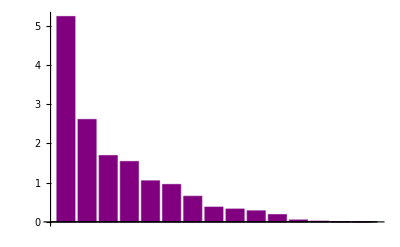

```mathematica
BarChart[varianceOfEachColumn,ChartStyle->Purple]
```

```mathematica
cumulativeVariance1=Accumulate[varianceOfEachColumn/Total@varianceOfEachColumn]
```

{0.349172,0.523386,0.636236,0.739001,0.808896,0.872623,0.916291,0.941539,0.963511,0.982447,0.994955,0.998365,0.999735,1.,1.}

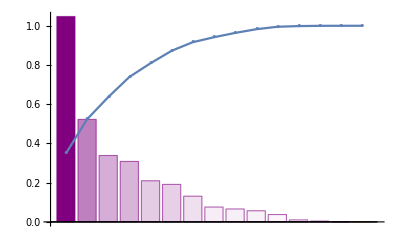

```mathematica
Show[{BarChart[1/5varianceOfEachColumn,ColorFunction ->Function[{height},Opacity[height]],ChartStyle->Purple],ListPlot[cumulativeVariance1,Joined->True,PlotMarkers->"•"]},PlotRange->All]
```

```mathematica
(*The cumulative variance is actually a bit worse than in the original paper. There, five principal components explained 82% of the variance, and here only 80%, so I may try for six-variable functions. That may be easier to analyze.*)
```

#### Normalized

```mathematica
PCAData2=Transpose[LogNormed]
```

(1.91145 | 1.25491 | 1.26095 | 1.23364 | 0.737543 | 0.986495 | 1.25276 | 1.3344 | 1.27274 | 1.31932 | 1.5724 | 1.43262 | 1.20242 | 0.653926 | 1.24099
1.40262 | 1.24516 | 1.24784 | 1.22056 | 0.725235 | 1.10975 | 1.25317 | 1.31072 | 1.30925 | 1.25624 | 1.62969 | 1.46501 | 1.33479 | 0.936955 | 1.18043
1.25414 | 1.22954 | 1.22688 | 1.22275 | 1.16259 | 1.09795 | 1.25478 | 1.26893 | 1.24058 | 1.23411 | 1.57945 | 1.38629 | 1.20242 | 0.863261 | 1.20077
1.26982 | 1.22926 | 1.2273 | 1.2224 | 1.15052 | 1.09795 | 1.25357 | 1.28743 | 1.24058 | 1.23411 | 1.68176 | 1.42435 | 1.20242 | 0.605636 | 1.19997
1.23822 | 1.2309 | 1.22581 | 1.22175 | 1.16259 | 1.09927 | 1.25397 | 1.25009 | 1.24303 | 1.23738 | 1.4785 | 1.36304 | 1.20242 | 0.881631 | 1.19671
1.41615 | 1.2496 | 1.21357 | 1.21093 | 1.17293 | 0.645591 | 1.25478 | 1.32846 | 1.29851 | 1.25357 | 1.71503 | 1.49122 | 1.33479 | 1.00659 | 1.34443
1.94034 | 1.25491 | 1.26121 | 1.23389 | 0.737543 | 0.986495 | 1.25357 | 1.31676 | 1.28532 | 1.33028 | 1.48367 | 1.37908 | 1.20242 | 0.562751 | 1.23765
1.28526 | 1.22914 | 1.22666 | 1.22265 | 1.16419 | 1.09267 | 1.25518 | 1.30559 | 1.24058 | 1.22892 | 1.77264 | 1.45968 | 1.20242 | -0.0682083 | 1.18822
1.3889 | 1.245 | 1.24914 | 1.2224 | 0.739987 | 0.684214 | 1.25276 | 1.29265 | 1.31306 | 1.26156 | 1.51162 | 1.43399 | 1.33479 | 0.917389 | 1.34036
1.3889 | 1.23996 | 1.24257 | 1.21936 | 0.816315 | 0.491268 | 1.25518 | 1.29265 | 1.32138 | 1.26156 | 1.54611 | 1.41323 | 1.33479 | 1.06698 | 1.31133
1.26847 | 1.23349 | 1.23069 | 1.2363 | 1.31233 | 1.35569 | 1.25518 | 1.27155 | 1.24385 | 1.24766 | 1.3633 | 1.31329 | 1.25276 | 0.988356 | 1.33318
1.23821 | 1.23237 | 1.22661 | 1.2227 | 1.16658 | 1.09663 | 1.25639 | 1.25009 | 1.24872 | 1.23793 | 1.49137 | 1.33015 | 1.20242 | 0.789955 | 1.07957
1.40262 | 1.24638 | 1.24289 | 1.21946 | 0.811782 | 0.488847 | 1.25276 | 1.31072 | 1.31685 | 1.2589 | 1.64953 | 1.45029 | 1.33479 | 1.06224 | 1.30986
1.22203 | 1.29233 | 1.23286 | 1.23014 | 1.19097 | 1.10714 | 1.25559 | 1.23089 | 1.25196 | 1.24172 | 1.3806 | 1.30553 | 1.20242 | 0.809708 | 1.0746
1.29737 | 1.24319 | 1.24372 | 1.24505 | 1.26439 | 1.2751 | 1.25518 | 1.28994 | 1.31609 | 1.28361 | 1.41707 | 1.41462 | 1.3007 | 0.781188 | 1.08108
1.28393 | 1.23241 | 1.22921 | 1.23409 | 1.30056 | 1.35976 | 1.25276 | 1.29 | 1.24385 | 1.24389 | 1.47591 | 1.35862 | 1.25276 | 0.718911 | 1.3133
1.37499 | 1.25171 | 1.24758 | 1.22439 | 0.821952 | 0.481547 | 1.25317 | 1.27426 | 1.32739 | 1.26686 | 1.41707 | 1.38053 | 1.33479 | 1.0527 | 1.31135
1.25228 | 1.25065 | 1.24602 | 1.25093 | 1.31783 | 1.33198 | 1.25276 | 1.25003 | 1.33038 | 1.28127 | 1.43617 | 1.41323 | 1.25276 | 0.865576 | 1.21839
1.28393 | 1.25065 | 1.25183 | 1.25262 | 1.26366 | 1.26622 | 1.25518 | 1.29 | 1.24385 | 1.24389 | 1.47591 | 1.35862 | 1.25276 | 0.962461 | 1.25207
1.25228 | 1.23241 | 1.22363 | 1.21896 | 1.15052 | 1.33198 | 1.25599 | 1.25003 | 1.33038 | 1.28127 | 1.43617 | 1.41183 | 1.25276 | 0.852777 | 1.16422
1.29915 | 1.23671 | 1.22868 | 1.23394 | 1.30543 | 1.35874 | 1.25518 | 1.30811 | 1.24303 | 1.24064 | 1.58645 | 1.39772 | 1.25276 | 0.856284 | 1.31632
1.26847 | 1.25065 | 1.25183 | 1.25247 | 1.26149 | 1.22063 | 1.25559 | 1.27155 | 1.25115 | 1.2482 | 1.37774 | 1.30085 | 1.25276 | 0.911885 | 1.25332
1.31284 | 1.25491 | 1.26203 | 1.25503 | 1.14971 | 1.27067 | 1.25559 | 1.31063 | 1.2414 | 1.2533 | 1.34275 | 1.31638 | 1.3007 | 0.773612 | 1.44762
1.28393 | 1.24744 | 1.24862 | 1.24875 | 1.2513 | 1.26511 | 1.25559 | 1.29 | 1.25034 | 1.24443 | 1.50155 | 1.34223 | 1.25276 | 1.02154 | 1.42967
1.3889 | 1.24532 | 1.25152 | 1.23098 | 0.885119 | 1.29694 | 1.25478 | 1.29265 | 1.32138 | 1.26156 | 1.54611 | 1.41323 | 1.33479 | 1.14601 | 1.44793
1.3889 | 1.24426 | 1.25514 | 1.23251 | 0.841986 | 1.29261 | 1.25317 | 1.29265 | 1.32138 | 1.26156 | 1.52408 | 1.42297 | 1.33479 | 0.826679 | 1.44899
1.37499 | 1.25276 | 1.25344 | 1.23197 | 0.864863 | 1.29694 | 1.25074 | 1.27426 | 1.32739 | 1.26686 | 1.41707 | 1.38053 | 1.33479 | 1.1337 | 1.44802
1.29737 | 1.24102 | 1.24016 | 1.23718 | 1.19408 | 1.28608 | 1.25074 | 1.28994 | 1.31609 | 1.28361 | 1.41707 | 1.41462 | 1.3007 | 0.781188 | 1.02062
1.3889 | 1.24209 | 1.24674 | 1.22424 | 0.836461 | 0.474194 | 1.25195 | 1.29265 | 1.32138 | 1.26156 | 1.52408 | 1.42297 | 1.33479 | 0.792445 | 1.31167
1.40262 | 1.24102 | 1.24132 | 1.21871 | 0.828675 | 0.483986 | 1.25518 | 1.31072 | 1.31685 | 1.2589 | 1.64076 | 1.45433 | 1.33479 | 0.814587 | 1.312
1.22203 | 1.24209 | 1.23817 | 1.24554 | 1.34418 | 1.38481 | 1.25518 | 1.23089 | 1.2471 | 1.24091 | 1.38345 | 1.3102 | 1.20242 | 0.668111 | 1.24635
1.14 | 1.27171 | 1.27567 | 1.27313 | 1.2373 | 1.16549 | 1.25276 | 1.16515 | 1.25115 | 1.21761 | 1.51413 | 1.35714 | 1.09342 | 0.702717 | 1.08355
1.41615 | 1.24102 | 1.24174 | 1.21886 | 0.821952 | 0.491268 | 1.25478 | 1.32846 | 1.31306 | 1.25357 | 1.74524 | 1.48604 | 1.33479 | 0.837438 | 1.45461
1.35607 | 1.2496 | 1.25622 | 1.24086 | 0.994009 | 1.26845 | 1.25478 | 1.36777 | 1.28766 | 1.2597 | 1.70887 | 1.49896 | 1.25276 | 0.423614 | 1.42437
1.25228 | 1.24854 | 1.24262 | 1.25073 | 1.35874 | 1.26622 | 1.25518 | 1.25003 | 1.33038 | 1.28127 | 1.43617 | 1.41183 | 1.25276 | 1.00156 | 1.2407
1.20507 | 1.24854 | 1.24079 | 1.23758 | 1.19097 | 1.33511 | 1.25317 | 1.20846 | 1.34961 | 1.27814 | 1.45491 | 1.41043 | 1.20242 | 0.928306 | 1.0884
1.29915 | 1.24638 | 1.2482 | 1.24855 | 1.25276 | 1.26622 | 1.25518 | 1.30811 | 1.24953 | 1.24091 | 1.60944 | 1.38197 | 1.25276 | 0.377608 | 1.42885
1.40262 | 1.24102 | 1.23838 | 1.23418 | 1.17293 | 1.30448 | 1.25438 | 1.31072 | 1.31685 | 1.2589 | 1.64076 | 1.45433 | 1.33479 | 0.848082 | 1.44874
1.40262 | 1.24638 | 1.25328 | 1.23088 | 0.845286 | 1.28826 | 1.25397 | 1.31072 | 1.31685 | 1.2589 | 1.61849 | 1.46368 | 1.33479 | 0.659624 | 1.44703
1.26847 | 1.25276 | 1.25281 | 1.25267 | 1.25057 | 1.24369 | 1.2576 | 1.27155 | 1.24385 | 1.24766 | 1.3633 | 1.31329 | 1.25276 | 1.27527 | 1.39993
1.28393 | 1.24532 | 1.2469 | 1.24695 | 1.24763 | 1.26064 | 1.25518 | 1.29 | 1.25034 | 1.24443 | 1.48881 | 1.34673 | 1.25276 | 0.791201 | 1.2459
1.26847 | 1.2496 | 1.25059 | 1.25073 | 1.25203 | 1.24824 | 1.25518 | 1.27155 | 1.25115 | 1.2482 | 1.37774 | 1.30085 | 1.25276 | 0.979111 | 1.24499
1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276
1.25276 | 1.2581 | 1.26285 | 1.25725 | 1.17452 | 1.30983 | 1.25397 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 0.917389 | 1.24505
1.22202 | 1.25171 | 1.24867 | 1.24962 | 1.26294 | 1.31302 | 1.2568 | 1.23089 | 1.2471 | 1.24091 | 1.38345 | 1.3102 | 1.20242 | 1.18539 | 1.31375
1.20557 | 1.25171 | 1.24862 | 1.24957 | 1.26366 | 1.31196 | 1.25518 | 1.21131 | 1.25759 | 1.24578 | 1.27524 | 1.24947 | 1.20242 | 1.15297 | 1.2946)

```mathematica
Dimensions[PCAData2]
```

{46,15}

```mathematica
PCA2=PrincipalComponents[PCAData2];
```

```mathematica
varianceOfEachColumn2=Variance/@Transpose@PCA2
```

{0.120408,0.0644793,0.028472,0.0145682,0.00791714,0.00650749,0.00236224,0.000842865,0.000197914,0.000168083,0.0000634228,0.0000547576,3.80047×10^-6,1.21186×10^-6,1.79546×10^-7}

```mathematica
Dimensions[varianceOfEachColumn2]
```

{15}

```mathematica
cumulativeVariance2=Accumulate[varianceOfEachColumn2/Total@varianceOfEachColumn2]
```

{0.48937,0.751432,0.86715,0.926359,0.958536,0.984985,0.994585,0.998011,0.998815,0.999499,0.999756,0.999979,0.999994,0.999999,1.}

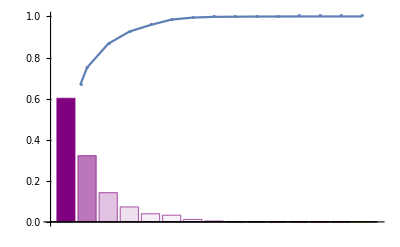

```mathematica
Show[{BarChart[5varianceOfEachColumn2,ColorFunction ->Function[{height},Opacity[height]],ChartStyle->Purple],ListPlot[cumulativeVariance2,Joined->True,PlotMarkers->"•"]},PlotRange->All]
```

### Correlation Matrix

The following matrix is a table of Pearson’s correlation coefficients (r values) between each chemical measurement.
High inter-correlation between a pair of characteristics can distort a linear regression analysis, so the authors decided to avoid any pair of characteristics with an absolute value of r greater than 0.8. 
Actual formula for correlation coefficient: Correl(X,Y) = [Sum((x-xbar)(y-ybar))]/[SqRt[(Sum(x-xbar)^2)(Sum(y-ybar)^2)]] where xbar and ybar are the averages of the data set for the respective measurements.

```mathematica
Correlation[DatatoUse]//MatrixForm
```

(1. | -0.0838851 | 0.271229 | 0.258482 | 0.606635 | 0.33373 | -0.251888 | -0.526888 | -0.194399 | -0.74975 | -0.240207 | 0.314001 | -0.120385 | 0.214991 | -0.141191 | -0.445075
-0.0838851 | 1. | -0.555216 | 0.460072 | -0.00474525 | 0.0222463 | 0.0328363 | -0.279507 | -0.0262394 | 0.0985546 | -0.353896 | 0.311367 | -0.165832 | 0.179423 | -0.0674399 | -0.264673
0.271229 | -0.555216 | 1. | -0.633469 | 0.25258 | -0.0991034 | -0.208526 | 0.0429598 | -0.0484502 | -0.239614 | 0.29755 | -0.218898 | 0.0103618 | -0.0981184 | -0.232514 | 0.37217
0.258482 | 0.460072 | -0.633469 | 1. | 0.588676 | 0.605684 | -0.14666 | -0.430435 | -0.383033 | -0.126844 | -0.5825 | 0.616822 | -0.448233 | 0.12625 | -0.0415513 | -0.577815
0.606635 | -0.00474525 | 0.25258 | 0.588676 | 1. | 0.653866 | -0.401401 | -0.493919 | -0.52948 | -0.408954 | -0.417618 | 0.542675 | -0.550087 | 0.0556044 | -0.295509 | -0.333557
0.33373 | 0.0222463 | -0.0991034 | 0.605684 | 0.653866 | 1. | -0.167066 | -0.325735 | -0.309641 | -0.110675 | -0.44131 | 0.429522 | -0.395825 | -0.00780498 | -0.0461461 | -0.352955
-0.251888 | 0.0328363 | -0.208526 | -0.14666 | -0.401401 | -0.167066 | 1. | 0.0568898 | 0.426957 | 0.334716 | 0.052511 | -0.272627 | 0.232715 | -0.0878039 | -0.0975939 | 0.196377
-0.526888 | -0.279507 | 0.0429598 | -0.430435 | -0.493919 | -0.325735 | 0.0568898 | 1. | 0.164145 | 0.290585 | 0.630205 | -0.62764 | 0.570061 | -0.31892 | 0.504224 | 0.342209
-0.194399 | -0.0262394 | -0.0484502 | -0.383033 | -0.52948 | -0.309641 | 0.426957 | 0.164145 | 1. | 0.578043 | 0.190174 | -0.61191 | 0.635146 | 0.130825 | 0.109751 | -0.0293615
-0.74975 | 0.0985546 | -0.239614 | -0.126844 | -0.408954 | -0.110675 | 0.334716 | 0.290585 | 0.578043 | 1. | -0.0841716 | -0.283039 | 0.219864 | -0.032633 | -0.0589038 | 0.199581
-0.240207 | -0.353896 | 0.29755 | -0.5825 | -0.417618 | -0.44131 | 0.052511 | 0.630205 | 0.190174 | -0.0841716 | 1. | -0.851108 | 0.243731 | -0.498631 | 0.235558 | 0.412785
0.314001 | 0.311367 | -0.218898 | 0.616822 | 0.542675 | 0.429522 | -0.272627 | -0.62764 | -0.61191 | -0.283039 | -0.851108 | 1. | -0.477366 | 0.385483 | -0.187162 | -0.405356
-0.120385 | -0.165832 | 0.0103618 | -0.448233 | -0.550087 | -0.395825 | 0.232715 | 0.570061 | 0.635146 | 0.219864 | 0.243731 | -0.477366 | 1. | 0.244028 | 0.544057 | -0.0169938
0.214991 | 0.179423 | -0.0981184 | 0.12625 | 0.0556044 | -0.00780498 | -0.0878039 | -0.31892 | 0.130825 | -0.032633 | -0.498631 | 0.385483 | 0.244028 | 1. | 0.175747 | -0.324742
-0.141191 | -0.0674399 | -0.232514 | -0.0415513 | -0.295509 | -0.0461461 | -0.0975939 | 0.504224 | 0.109751 | -0.0589038 | 0.235558 | -0.187162 | 0.544057 | 0.175747 | 1. | -0.23465
-0.445075 | -0.264673 | 0.37217 | -0.577815 | -0.333557 | -0.352955 | 0.196377 | 0.342209 | -0.0293615 | 0.199581 | 0.412785 | -0.405356 | -0.0169938 | -0.324742 | -0.23465 | 1.)

As I suspected, cLogP and Solubility are too highly correlated. Since the correlation with LogMU is *slightly* better for cLogP, I’ll remove Solubility. Then I’ll have 7 DFT and 7 physicochemical descriptors to continue with.

```mathematica
goodDataNew=ReplacePart[DatatoUse,{_,-5}->Nothing];
```

```mathematica
NormalizedCorrelation=Correlation[LogNormedT]
```

(1. | 0.0518339 | 0.251791 | -0.320389 | -0.683568 | -0.356071 | -0.268291 | 0.600373 | 0.258648 | 0.734481 | 0.30927 | 0.384649 | 0.232142 | -0.182151 | 0.220471 | 0.447899
0.0518339 | 1. | 0.560708 | 0.463043 | -0.0105159 | 0.0388608 | -0.0346917 | -0.287144 | -0.0203707 | 0.10078 | -0.360459 | -0.316652 | -0.170701 | 0.194279 | -0.0745413 | -0.269327
0.251791 | 0.560708 | 1. | 0.632436 | -0.265502 | 0.102595 | -0.208315 | -0.0515742 | 0.0533697 | 0.23857 | -0.296292 | -0.221319 | -0.0172655 | 0.0993527 | 0.226868 | -0.374426
-0.320389 | 0.463043 | 0.632436 | 1. | 0.577299 | 0.603713 | 0.146567 | -0.43434 | -0.383587 | -0.127169 | -0.590304 | -0.617767 | -0.44477 | 0.113199 | -0.0431225 | -0.57844
-0.683568 | -0.0105159 | -0.265502 | 0.577299 | 1. | 0.643925 | 0.406938 | -0.488672 | -0.537211 | -0.430406 | -0.416801 | -0.535936 | -0.536179 | 0.0310877 | -0.291856 | -0.340686
-0.356071 | 0.0388608 | 0.102595 | 0.603713 | 0.643925 | 1. | 0.170155 | -0.320456 | -0.349668 | -0.110512 | -0.423079 | -0.425419 | -0.426793 | -0.0485813 | -0.0974645 | -0.302178
-0.268291 | -0.0346917 | -0.208315 | 0.146567 | 0.406938 | 0.170155 | 1. | -0.0542261 | -0.427583 | -0.335566 | -0.062661 | -0.275892 | -0.22072 | 0.0463121 | 0.105708 | -0.196188
0.600373 | -0.287144 | -0.0515742 | -0.43434 | -0.488672 | -0.320456 | -0.0542261 | 1. | 0.168586 | 0.293796 | 0.616097 | 0.613338 | 0.587975 | -0.313457 | 0.504818 | 0.344723
0.258648 | -0.0203707 | 0.0533697 | -0.383587 | -0.537211 | -0.349668 | -0.427583 | 0.168586 | 1. | 0.589934 | 0.210658 | 0.615484 | 0.628864 | 0.173094 | 0.0955558 | -0.0286117
0.734481 | 0.10078 | 0.23857 | -0.127169 | -0.430406 | -0.110512 | -0.335566 | 0.293796 | 0.589934 | 1. | -0.0686565 | 0.290484 | 0.238551 | 0.01812 | -0.0548638 | 0.193277
0.30927 | -0.360459 | -0.296292 | -0.590304 | -0.416801 | -0.423079 | -0.062661 | 0.616097 | 0.210658 | -0.0686565 | 1. | 0.859958 | 0.236764 | -0.512295 | 0.222822 | 0.435485
0.384649 | -0.316652 | -0.221319 | -0.617767 | -0.535936 | -0.425419 | -0.275892 | 0.613338 | 0.615484 | 0.290484 | 0.859958 | 1. | 0.46306 | -0.370718 | 0.167504 | 0.417718
0.232142 | -0.170701 | -0.0172655 | -0.44477 | -0.536179 | -0.426793 | -0.22072 | 0.587975 | 0.628864 | 0.238551 | 0.236764 | 0.46306 | 1. | 0.269034 | 0.53788 | -0.0194828
-0.182151 | 0.194279 | 0.0993527 | 0.113199 | 0.0310877 | -0.0485813 | 0.0463121 | -0.313457 | 0.173094 | 0.01812 | -0.512295 | -0.370718 | 0.269034 | 1. | 0.154176 | -0.292823
0.220471 | -0.0745413 | 0.226868 | -0.0431225 | -0.291856 | -0.0974645 | 0.105708 | 0.504818 | 0.0955558 | -0.0548638 | 0.222822 | 0.167504 | 0.53788 | 0.154176 | 1. | -0.225222
0.447899 | -0.269327 | -0.374426 | -0.57844 | -0.340686 | -0.302178 | -0.196188 | 0.344723 | -0.0286117 | 0.193277 | 0.435485 | 0.417718 | -0.0194828 | -0.292823 | -0.225222 | 1.)

```mathematica
goodDataNormalized=ReplacePart[LogNormedT,{_,-5}-> Nothing];
```

### “Backwards” Regression Analysis

This could get intense. If I want to search 14 variables for the combination of six variables that best predicts logMU based on R^2 value, that will be 14C6 = 3003 combinations. The prior analysis searched 12C5 = 792 combinations and that just took a few seconds to run, so I might be OK.

```mathematica
whichParametersNew=Subsets[Range[Length@First@goodDataNew-1],{6}];
```

```mathematica
Length[whichParametersNew]
```

3003

```mathematica
whichParametersNew2=Append[#,-1]&/@whichParametersNew;
```

```mathematica
Length[whichParametersNew2]
```

3003

```mathematica
test1=whichParametersNew2[[1]]
```

{1,2,3,4,5,6,-1}

```mathematica
test2=Part[goodDataNew,All,test1];
```

```mathematica
Length[test2]
```

46

```mathematica
LinearModelFit[test2,Table[x[i],{i,1,6}],Table[x[i],{i,1,6}]]["RSquared"]
```

0.489373

```mathematica
allRSquared=MapIndexed[
Function[
{parameters,index},
regressThese=Part[goodDataNew,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,6}],Table[x[i],{i,1,6}]]["RSquared"]
],
whichParametersNew2
];
```

```mathematica
Length[allRSquared]
```

3003

```mathematica
bestFits=TakeLargestBy[allRSquared,Last,UpTo[5]]
```

{2760→0.635003,987→0.628417,970→0.626159,990→0.61956,864→0.618666}

These are actually terrible! I took away one of the DFT descriptors that ended up in the final models in Aouidate, et al - the DFT DM. So maybe that’s why. Just out of curiosity:

```mathematica
whichParametersNew2[[{2760,987,970,990,864}]]
```

(4 | 7 | 9 | 10 | 11 | 14 | -1
1 | 4 | 7 | 9 | 11 | 14 | -1
1 | 4 | 7 | 8 | 9 | 14 | -1
1 | 4 | 7 | 9 | 13 | 14 | -1
1 | 4 | 5 | 7 | 9 | 14 | -1)

DFT: 1 is Etotal, 4 is absolute hardness, 7 is Qmin, and 5 is Elumo. Physicochemical: 9 is surface tension, 10 is density, 11 is cLogP, 13 is “Druglikeness” score, and 14 is Dipole Moment from Millsian.

```mathematica
(*Whelp, now I'm inclined to try again with a data set that includes the Dipole Moment from DFT.*)
```

#### Normalized

```mathematica
whichParametersNew3=Subsets[Range[Length@First@goodDataNormalized-1],{6}];
```

```mathematica
Length[whichParametersNew3]
```

3003

```mathematica
whichParametersNew4=Append[#,-1]&/@whichParametersNew3;
```

```mathematica
Length[whichParametersNew4]
```

3003

```mathematica
test1=whichParametersNew4[[1]]
```

{1,2,3,4,5,6,-1}

```mathematica
test2=Part[goodDataNormalized,All,test1];
```

```mathematica
Length[test2]
```

46

```mathematica
LinearModelFit[test2,Table[x[i],{i,1,6}],Table[x[i],{i,1,6}]]["RSquared"]
```

0.477101

```mathematica
allRSquared2=MapIndexed[
Function[
{parameters,index},
regressThese=Part[goodDataNormalized,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,6}],Table[x[i],{i,1,6}]]["RSquared"]
],
whichParametersNew4
];
```

```mathematica
Length[allRSquared2]
```

3003

```mathematica
bestFits=TakeLargestBy[allRSquared,Last,UpTo[5]]
```

{492→0.62048,460→0.619288,1738→0.61707,291→0.611608,475→0.610837}

```mathematica
(*Whelp, now I'm inclined to try again with a data set that includes the Dipole Moment from DFT.*)
```

```mathematica
whichParametersNew4[[{492,460,1738,291,475}]]
```

(1 | 2 | 10 | 11 | 12 | 14 | -1
1 | 2 | 7 | 12 | 13 | 14 | -1
2 | 4 | 6 | 9 | 10 | 11 | -1
1 | 2 | 5 | 6 | 7 | 13 | -1
1 | 2 | 8 | 10 | 12 | 14 | -1)

# Second-Generation Data Set 2

```mathematica
newdata2=Import["/Users/themarchhare/Documents/GitHub/Project/Molecular Structures Real/Descriptors 2.xlsx"];
```

```mathematica
newdata2touse=Part[newdata2,3]
```

(ET | IP | EHOMO | η | ELUMO | Qp | DM | MW | γ | D | cLogP | TPSA | Druglikeness | logMU
−82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 0.046 | 3.242 | 274.154 | 37.9 | 1.324 | 2.04 | 44.48 | -2.1 | 2.72
−30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 0.135 | 1.996 | 255.376 | 42.6 | 1.08 | 2.29 | 69.78 | 0.19 | 1.96
−19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 0.126 | 1.234 | 223.311 | 33.9 | 0.998 | 2.07 | 44.48 | -0.47 | 2.02
−20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 0.126 | 1.283 | 237.338 | 33.9 | 0.998 | 2.53 | 44.48 | -2.43 | 1.95
−18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 0.127 | 1.117 | 209.285 | 34.2 | 1.01 | 1.66 | 44.48 | -0.31 | 1.9
−31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | −0.150 | 2.498 | 269.403 | 41.2 | 1.07 | 2.69 | 69.78 | 0.86 | 1.71
−86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 0.046 | 3.271 | 260.128 | 39.5 | 1.368 | 1.68 | 44.48 | -2.71 | 1.69
−21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 0.122 | 1.25 | 251.365 | 33.9 | 0.979 | 2.98 | 44.48 | -5.7 | 1.68
−29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | −0.131 | 2.115 | 241.35 | 43.1 | 1.1 | 1.79 | 69.78 | 0.01 | 1.66
−29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | −0.219 | 4.017 | 241.35 | 44.2 | 1.1 | 1.93 | 69.78 | 1.48 | 1.36
−20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 0.349 | 3.159 | 225.284 | 34.3 | 1.048 | 1.24 | 53.71 | 0.68 | 1.33
−18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 0.125 | 1.323 | 209.285 | 34.9 | 1.012 | 1.71 | 44.48 | -1.08 | 1.25
−30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | −0.220 | 4.084 | 255.376 | 43.6 | 1.09 | 2.38 | 69.78 | 1.43 | 1.29
−17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 0.133 | 1.618 | 195.258 | 35.3 | 1.026 | 1.3 | 44.48 | -0.92 | 1.27
−22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 0.273 | 1.297 | 239.268 | 43.5 | 1.184 | 1.43 | 62.94 | -1.15 | 1.14
−21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 0.353 | 3.234 | 239.311 | 34.3 | 1.034 | 1.65 | 53.71 | -1.63 | 1.36
−28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | −0.223 | 4.378 | 227.323 | 45. | 1.12 | 1.43 | 69.78 | 1.33 | 1.11
−19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 0.326 | 1.539 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | -0.45 | 1.
−21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 0.265 | 3.041 | 239.311 | 34.3 | 1.034 | 1.65 | 53.71 | 0.43 | 1.05
−19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 0.326 | 1.505 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | -0.56 | 1.
−22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 0.352 | 3.276 | 253.337 | 34.2 | 1.022 | 2.1 | 53.71 | -0.53 | 1.38
−20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 0.225 | 3.089 | 225.284 | 35.2 | 1.05 | 1.29 | 53.71 | -0.04 | 0.87
−23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 0.269 | 1.288 | 255.31 | 34. | 1.069 | 1.17 | 62.94 | -1.21 | 0.86
−21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 0.264 | 2.994 | 239.311 | 35.1 | 1.036 | 1.75 | 53.71 | 1.01 | 0.83
−29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 0.293 | 3.92 | 241.35 | 44.2 | 1.1 | 1.93 | 69.78 | 2.35 | 0.84
−29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 0.289 | 3.714 | 241.35 | 44.2 | 1.1 | 1.84 | 69.78 | -0.78 | 0.84
−28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 0.293 | 4.009 | 227.323 | 45. | 1.12 | 1.43 | 69.78 | 2.21 | 0.81
−22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.283 | 0.427 | 239.268 | 43.5 | 1.184 | 1.43 | 62.94 | -1.15 | 0.76
−29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | −0.226 | 4.42 | 241.35 | 44.2 | 1.1 | 1.84 | 69.78 | -1.06 | 0.66
−30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | −0.222 | 4.043 | 255.376 | 43.6 | 1.09 | 2.34 | 69.78 | -0.88 | 0.68
−17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 0.378 | 2.553 | 195.258 | 34.7 | 1.023 | 1.31 | 44.48 | -2. | 0.67
−12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 0.179 | 1.567 | 149.233 | 35.2 | 0.938 | 1.8 | 26.02 | -1.75 | 0.59
−31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | −0.219 | 4.067 | 269.403 | 43.1 | 1.07 | 2.84 | 69.78 | -0.69 | 0.58
−26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 0.267 | 3.375 | 301.38 | 39.8 | 1.093 | 2.66 | 53.71 | -3.54 | 0.46
−19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 0.265 | 1.369 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | 0.81 | 0.43
−16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 0.329 | 1.899 | 179.216 | 48. | 1.163 | 1.57 | 44.48 | 0.11 | 0.41
−22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 0.265 | 2.947 | 253.337 | 35. | 1.023 | 2.2 | 53.71 | -3.79 | 0.38
−30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 0.3 | 3.05 | 255.376 | 43.6 | 1.09 | 2.34 | 69.78 | -0.6 | 0.38
−30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 0.285 | 3.751 | 255.376 | 43.6 | 1.09 | 2.24 | 69.78 | -2.06 | 0.38
−20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 0.245 | 3.136 | 225.284 | 34.3 | 1.048 | 1.24 | 53.71 | 3.93 | 0.33
−21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 0.26 | 2.979 | 239.311 | 35.1 | 1.036 | 1.7 | 53.71 | -1.07 | 0.23
−20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 0.249 | 3.237 | 225.284 | 35.2 | 1.05 | 1.29 | 53.71 | 0.59 | 0.03
−19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 0.253 | 3.203 | 211.258 | 35.4 | 1.067 | 0.88 | 53.71 | 3.64 | 0.
−19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 0.305 | 1.449 | 211.258 | 35.4 | 1.067 | 0.88 | 53.71 | 0.01 | −0.030
−17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 0.308 | 3.673 | 195.258 | 34.7 | 1.023 | 1.31 | 44.48 | 2.81 | −0.060
−16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 0.307 | 3.724 | 181.232 | 36. | 1.041 | 0.95 | 44.48 | 2.43 | −0.670
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  | )

List of variables:

```mathematica
newdata2touse[[1]]
```

{ET,IP,EHOMO,η,ELUMO,Qp,DM,MW,γ,D,cLogP,TPSA,Druglikeness,logMU}

```mathematica
JustNumbers=Part[newdata2touse,2;;-18]
```

(−82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 0.046 | 3.242 | 274.154 | 37.9 | 1.324 | 2.04 | 44.48 | -2.1 | 2.72
−30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 0.135 | 1.996 | 255.376 | 42.6 | 1.08 | 2.29 | 69.78 | 0.19 | 1.96
−19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 0.126 | 1.234 | 223.311 | 33.9 | 0.998 | 2.07 | 44.48 | -0.47 | 2.02
−20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 0.126 | 1.283 | 237.338 | 33.9 | 0.998 | 2.53 | 44.48 | -2.43 | 1.95
−18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 0.127 | 1.117 | 209.285 | 34.2 | 1.01 | 1.66 | 44.48 | -0.31 | 1.9
−31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | −0.150 | 2.498 | 269.403 | 41.2 | 1.07 | 2.69 | 69.78 | 0.86 | 1.71
−86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 0.046 | 3.271 | 260.128 | 39.5 | 1.368 | 1.68 | 44.48 | -2.71 | 1.69
−21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 0.122 | 1.25 | 251.365 | 33.9 | 0.979 | 2.98 | 44.48 | -5.7 | 1.68
−29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | −0.131 | 2.115 | 241.35 | 43.1 | 1.1 | 1.79 | 69.78 | 0.01 | 1.66
−29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | −0.219 | 4.017 | 241.35 | 44.2 | 1.1 | 1.93 | 69.78 | 1.48 | 1.36
−20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 0.349 | 3.159 | 225.284 | 34.3 | 1.048 | 1.24 | 53.71 | 0.68 | 1.33
−18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 0.125 | 1.323 | 209.285 | 34.9 | 1.012 | 1.71 | 44.48 | -1.08 | 1.25
−30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | −0.220 | 4.084 | 255.376 | 43.6 | 1.09 | 2.38 | 69.78 | 1.43 | 1.29
−17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 0.133 | 1.618 | 195.258 | 35.3 | 1.026 | 1.3 | 44.48 | -0.92 | 1.27
−22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 0.273 | 1.297 | 239.268 | 43.5 | 1.184 | 1.43 | 62.94 | -1.15 | 1.14
−21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 0.353 | 3.234 | 239.311 | 34.3 | 1.034 | 1.65 | 53.71 | -1.63 | 1.36
−28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | −0.223 | 4.378 | 227.323 | 45. | 1.12 | 1.43 | 69.78 | 1.33 | 1.11
−19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 0.326 | 1.539 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | -0.45 | 1.
−21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 0.265 | 3.041 | 239.311 | 34.3 | 1.034 | 1.65 | 53.71 | 0.43 | 1.05
−19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 0.326 | 1.505 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | -0.56 | 1.
−22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 0.352 | 3.276 | 253.337 | 34.2 | 1.022 | 2.1 | 53.71 | -0.53 | 1.38
−20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 0.225 | 3.089 | 225.284 | 35.2 | 1.05 | 1.29 | 53.71 | -0.04 | 0.87
−23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 0.269 | 1.288 | 255.31 | 34. | 1.069 | 1.17 | 62.94 | -1.21 | 0.86
−21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 0.264 | 2.994 | 239.311 | 35.1 | 1.036 | 1.75 | 53.71 | 1.01 | 0.83
−29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 0.293 | 3.92 | 241.35 | 44.2 | 1.1 | 1.93 | 69.78 | 2.35 | 0.84
−29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 0.289 | 3.714 | 241.35 | 44.2 | 1.1 | 1.84 | 69.78 | -0.78 | 0.84
−28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 0.293 | 4.009 | 227.323 | 45. | 1.12 | 1.43 | 69.78 | 2.21 | 0.81
−22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.283 | 0.427 | 239.268 | 43.5 | 1.184 | 1.43 | 62.94 | -1.15 | 0.76
−29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | −0.226 | 4.42 | 241.35 | 44.2 | 1.1 | 1.84 | 69.78 | -1.06 | 0.66
−30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | −0.222 | 4.043 | 255.376 | 43.6 | 1.09 | 2.34 | 69.78 | -0.88 | 0.68
−17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 0.378 | 2.553 | 195.258 | 34.7 | 1.023 | 1.31 | 44.48 | -2. | 0.67
−12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 0.179 | 1.567 | 149.233 | 35.2 | 0.938 | 1.8 | 26.02 | -1.75 | 0.59
−31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | −0.219 | 4.067 | 269.403 | 43.1 | 1.07 | 2.84 | 69.78 | -0.69 | 0.58
−26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 0.267 | 3.375 | 301.38 | 39.8 | 1.093 | 2.66 | 53.71 | -3.54 | 0.46
−19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 0.265 | 1.369 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | 0.81 | 0.43
−16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 0.329 | 1.899 | 179.216 | 48. | 1.163 | 1.57 | 44.48 | 0.11 | 0.41
−22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 0.265 | 2.947 | 253.337 | 35. | 1.023 | 2.2 | 53.71 | -3.79 | 0.38
−30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 0.3 | 3.05 | 255.376 | 43.6 | 1.09 | 2.34 | 69.78 | -0.6 | 0.38
−30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 0.285 | 3.751 | 255.376 | 43.6 | 1.09 | 2.24 | 69.78 | -2.06 | 0.38
−20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 0.245 | 3.136 | 225.284 | 34.3 | 1.048 | 1.24 | 53.71 | 3.93 | 0.33
−21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 0.26 | 2.979 | 239.311 | 35.1 | 1.036 | 1.7 | 53.71 | -1.07 | 0.23
−20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 0.249 | 3.237 | 225.284 | 35.2 | 1.05 | 1.29 | 53.71 | 0.59 | 0.03
−19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 0.253 | 3.203 | 211.258 | 35.4 | 1.067 | 0.88 | 53.71 | 3.64 | 0.
−19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 0.305 | 1.449 | 211.258 | 35.4 | 1.067 | 0.88 | 53.71 | 0.01 | −0.030
−17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 0.308 | 3.673 | 195.258 | 34.7 | 1.023 | 1.31 | 44.48 | 2.81 | −0.060
−16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 0.307 | 3.724 | 181.232 | 36. | 1.041 | 0.95 | 44.48 | 2.43 | −0.670)

```mathematica
DatatoUse2=ReplaceAll[JustNumbers,s_String:>ToExpression[s]];
```

### Normalization

```mathematica
g[list_]:=list/list[[43]]
transform[n_]:=Log[n+2.5]
```

```mathematica
ToNormalize2=Transpose[DatatoUse2[[All,1;;-2]]]
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.04 | 2.29 | 2.07 | 2.53 | 1.66 | 2.69 | 1.68 | 2.98 | 1.79 | 1.93 | 1.24 | 1.71 | 2.38 | 1.3 | 1.43 | 1.65 | 1.43 | 1.5 | 1.65 | 1.5 | 2.1 | 1.29 | 1.17 | 1.75 | 1.93 | 1.84 | 1.43 | 1.43 | 1.84 | 2.34 | 1.31 | 1.8 | 2.84 | 2.66 | 1.5 | 1.57 | 2.2 | 2.34 | 2.24 | 1.24 | 1.7 | 1.29 | 0.88 | 0.88 | 1.31 | 0.95
44.48 | 69.78 | 44.48 | 44.48 | 44.48 | 69.78 | 44.48 | 44.48 | 69.78 | 69.78 | 53.71 | 44.48 | 69.78 | 44.48 | 62.94 | 53.71 | 69.78 | 53.71 | 53.71 | 53.71 | 53.71 | 53.71 | 62.94 | 53.71 | 69.78 | 69.78 | 69.78 | 62.94 | 69.78 | 69.78 | 44.48 | 26.02 | 69.78 | 53.71 | 53.71 | 44.48 | 53.71 | 69.78 | 69.78 | 53.71 | 53.71 | 53.71 | 53.71 | 53.71 | 44.48 | 44.48
-2.1 | 0.19 | -0.47 | -2.43 | -0.31 | 0.86 | -2.71 | -5.7 | 0.01 | 1.48 | 0.68 | -1.08 | 1.43 | -0.92 | -1.15 | -1.63 | 1.33 | -0.45 | 0.43 | -0.56 | -0.53 | -0.04 | -1.21 | 1.01 | 2.35 | -0.78 | 2.21 | -1.15 | -1.06 | -0.88 | -2. | -1.75 | -0.69 | -3.54 | 0.81 | 0.11 | -3.79 | -0.6 | -2.06 | 3.93 | -1.07 | 0.59 | 3.64 | 0.01 | 2.81 | 2.43)

```mathematica
Dimensions[ToNormalize2]
```

{13,46}

```mathematica
RatioNormalized2=Map[g,ToNormalize2]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1.01218 | 0.623166 | 0.385264 | 0.400562 | 0.348736 | 0.779894 | 1.02123 | 0.390259 | 0.660318 | 1.25414 | 0.986263 | 0.41305 | 1.27505 | 0.505151 | 0.404933 | 1.00968 | 1.36684 | 0.480487 | 0.949422 | 0.469872 | 1.02279 | 0.964408 | 0.402123 | 0.934749 | 1.22385 | 1.15954 | 1.25164 | 0.133313 | 1.37996 | 1.26225 | 0.797065 | 0.489229 | 1.26975 | 1.0537 | 0.427412 | 0.592882 | 0.920075 | 0.952232 | 1.17109 | 0.979082 | 0.930066 | 1.01062 | 1. | 0.452388 | 1.14674 | 1.16266
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
2.31818 | 2.60227 | 2.35227 | 2.875 | 1.88636 | 3.05682 | 1.90909 | 3.38636 | 2.03409 | 2.19318 | 1.40909 | 1.94318 | 2.70455 | 1.47727 | 1.625 | 1.875 | 1.625 | 1.70455 | 1.875 | 1.70455 | 2.38636 | 1.46591 | 1.32955 | 1.98864 | 2.19318 | 2.09091 | 1.625 | 1.625 | 2.09091 | 2.65909 | 1.48864 | 2.04545 | 3.22727 | 3.02273 | 1.70455 | 1.78409 | 2.5 | 2.65909 | 2.54545 | 1.40909 | 1.93182 | 1.46591 | 1. | 1. | 1.48864 | 1.07955
0.828151 | 1.2992 | 0.828151 | 0.828151 | 0.828151 | 1.2992 | 0.828151 | 0.828151 | 1.2992 | 1.2992 | 1. | 0.828151 | 1.2992 | 0.828151 | 1.17185 | 1. | 1.2992 | 1. | 1. | 1. | 1. | 1. | 1.17185 | 1. | 1.2992 | 1.2992 | 1.2992 | 1.17185 | 1.2992 | 1.2992 | 0.828151 | 0.484454 | 1.2992 | 1. | 1. | 0.828151 | 1. | 1.2992 | 1.2992 | 1. | 1. | 1. | 1. | 1. | 0.828151 | 0.828151
-0.576923 | 0.0521978 | -0.129121 | -0.667582 | -0.0851648 | 0.236264 | -0.744505 | -1.56593 | 0.00274725 | 0.406593 | 0.186813 | -0.296703 | 0.392857 | -0.252747 | -0.315934 | -0.447802 | 0.365385 | -0.123626 | 0.118132 | -0.153846 | -0.145604 | -0.010989 | -0.332418 | 0.277473 | 0.645604 | -0.214286 | 0.607143 | -0.315934 | -0.291209 | -0.241758 | -0.549451 | -0.480769 | -0.18956 | -0.972527 | 0.222527 | 0.0302198 | -1.04121 | -0.164835 | -0.565934 | 1.07967 | -0.293956 | 0.162088 | 1. | 0.00274725 | 0.771978 | 0.667582)

```mathematica
Dimensions[RatioNormalized2]
```

{13,46}

```mathematica
RatioNormalizedFinal2=Append[RatioNormalized2,logMUs]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1.01218 | 0.623166 | 0.385264 | 0.400562 | 0.348736 | 0.779894 | 1.02123 | 0.390259 | 0.660318 | 1.25414 | 0.986263 | 0.41305 | 1.27505 | 0.505151 | 0.404933 | 1.00968 | 1.36684 | 0.480487 | 0.949422 | 0.469872 | 1.02279 | 0.964408 | 0.402123 | 0.934749 | 1.22385 | 1.15954 | 1.25164 | 0.133313 | 1.37996 | 1.26225 | 0.797065 | 0.489229 | 1.26975 | 1.0537 | 0.427412 | 0.592882 | 0.920075 | 0.952232 | 1.17109 | 0.979082 | 0.930066 | 1.01062 | 1. | 0.452388 | 1.14674 | 1.16266
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
2.31818 | 2.60227 | 2.35227 | 2.875 | 1.88636 | 3.05682 | 1.90909 | 3.38636 | 2.03409 | 2.19318 | 1.40909 | 1.94318 | 2.70455 | 1.47727 | 1.625 | 1.875 | 1.625 | 1.70455 | 1.875 | 1.70455 | 2.38636 | 1.46591 | 1.32955 | 1.98864 | 2.19318 | 2.09091 | 1.625 | 1.625 | 2.09091 | 2.65909 | 1.48864 | 2.04545 | 3.22727 | 3.02273 | 1.70455 | 1.78409 | 2.5 | 2.65909 | 2.54545 | 1.40909 | 1.93182 | 1.46591 | 1. | 1. | 1.48864 | 1.07955
0.828151 | 1.2992 | 0.828151 | 0.828151 | 0.828151 | 1.2992 | 0.828151 | 0.828151 | 1.2992 | 1.2992 | 1. | 0.828151 | 1.2992 | 0.828151 | 1.17185 | 1. | 1.2992 | 1. | 1. | 1. | 1. | 1. | 1.17185 | 1. | 1.2992 | 1.2992 | 1.2992 | 1.17185 | 1.2992 | 1.2992 | 0.828151 | 0.484454 | 1.2992 | 1. | 1. | 0.828151 | 1. | 1.2992 | 1.2992 | 1. | 1. | 1. | 1. | 1. | 0.828151 | 0.828151
-0.576923 | 0.0521978 | -0.129121 | -0.667582 | -0.0851648 | 0.236264 | -0.744505 | -1.56593 | 0.00274725 | 0.406593 | 0.186813 | -0.296703 | 0.392857 | -0.252747 | -0.315934 | -0.447802 | 0.365385 | -0.123626 | 0.118132 | -0.153846 | -0.145604 | -0.010989 | -0.332418 | 0.277473 | 0.645604 | -0.214286 | 0.607143 | -0.315934 | -0.291209 | -0.241758 | -0.549451 | -0.480769 | -0.18956 | -0.972527 | 0.222527 | 0.0302198 | -1.04121 | -0.164835 | -0.565934 | 1.07967 | -0.293956 | 0.162088 | 1. | 0.00274725 | 0.771978 | 0.667582
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
LogNormed2=Map[transform,RatioNormalized2]
```

(1.91145 | 1.40262 | 1.25414 | 1.26982 | 1.23822 | 1.41615 | 1.94034 | 1.28526 | 1.3889 | 1.3889 | 1.26847 | 1.23821 | 1.40262 | 1.22203 | 1.29737 | 1.28393 | 1.37499 | 1.25228 | 1.28393 | 1.25228 | 1.29915 | 1.26847 | 1.31284 | 1.28393 | 1.3889 | 1.3889 | 1.37499 | 1.29737 | 1.3889 | 1.40262 | 1.22203 | 1.14 | 1.41615 | 1.35607 | 1.25228 | 1.20507 | 1.29915 | 1.40262 | 1.40262 | 1.26847 | 1.28393 | 1.26847 | 1.25276 | 1.25276 | 1.22202 | 1.20557
1.25491 | 1.24516 | 1.22954 | 1.22926 | 1.2309 | 1.2496 | 1.25491 | 1.22914 | 1.245 | 1.23996 | 1.23349 | 1.23237 | 1.24638 | 1.29233 | 1.24319 | 1.23241 | 1.25171 | 1.25065 | 1.25065 | 1.23241 | 1.23671 | 1.25065 | 1.25491 | 1.24744 | 1.24532 | 1.24426 | 1.25276 | 1.24102 | 1.24209 | 1.24102 | 1.24209 | 1.27171 | 1.24102 | 1.2496 | 1.24854 | 1.24854 | 1.24638 | 1.24102 | 1.24638 | 1.25276 | 1.24532 | 1.2496 | 1.25276 | 1.2581 | 1.25171 | 1.25171
1.26095 | 1.24784 | 1.22688 | 1.2273 | 1.22581 | 1.21357 | 1.26121 | 1.22666 | 1.24914 | 1.24257 | 1.23069 | 1.22661 | 1.24289 | 1.23286 | 1.24372 | 1.22921 | 1.24758 | 1.24602 | 1.25183 | 1.22363 | 1.22868 | 1.25183 | 1.26203 | 1.24862 | 1.25152 | 1.25514 | 1.25344 | 1.24016 | 1.24674 | 1.24132 | 1.23817 | 1.27567 | 1.24174 | 1.25622 | 1.24262 | 1.24079 | 1.2482 | 1.23838 | 1.25328 | 1.25281 | 1.2469 | 1.25059 | 1.25276 | 1.26285 | 1.24867 | 1.24862
1.23364 | 1.22056 | 1.22275 | 1.2224 | 1.22175 | 1.21093 | 1.23389 | 1.22265 | 1.2224 | 1.21936 | 1.2363 | 1.2227 | 1.21946 | 1.23014 | 1.24505 | 1.23409 | 1.22439 | 1.25093 | 1.25262 | 1.21896 | 1.23394 | 1.25247 | 1.25503 | 1.24875 | 1.23098 | 1.23251 | 1.23197 | 1.23718 | 1.22424 | 1.21871 | 1.24554 | 1.27313 | 1.21886 | 1.24086 | 1.25073 | 1.23758 | 1.24855 | 1.23418 | 1.23088 | 1.25267 | 1.24695 | 1.25073 | 1.25276 | 1.25725 | 1.24962 | 1.24957
0.737543 | 0.725235 | 1.16259 | 1.15052 | 1.16259 | 1.17293 | 0.737543 | 1.16419 | 0.739987 | 0.816315 | 1.31233 | 1.16658 | 0.811782 | 1.19097 | 1.26439 | 1.30056 | 0.821952 | 1.31783 | 1.26366 | 1.15052 | 1.30543 | 1.26149 | 1.14971 | 1.2513 | 0.885119 | 0.841986 | 0.864863 | 1.19408 | 0.836461 | 0.828675 | 1.34418 | 1.2373 | 0.821952 | 0.994009 | 1.35874 | 1.19097 | 1.25276 | 1.17293 | 0.845286 | 1.25057 | 1.24763 | 1.25203 | 1.25276 | 1.17452 | 1.26294 | 1.26366
0.986495 | 1.10975 | 1.09795 | 1.09795 | 1.09927 | 0.645591 | 0.986495 | 1.09267 | 0.684214 | 0.491268 | 1.35569 | 1.09663 | 0.488847 | 1.10714 | 1.2751 | 1.35976 | 0.481547 | 1.33198 | 1.26622 | 1.33198 | 1.35874 | 1.22063 | 1.27067 | 1.26511 | 1.29694 | 1.29261 | 1.29694 | 1.28608 | 0.474194 | 0.483986 | 1.38481 | 1.16549 | 0.491268 | 1.26845 | 1.26622 | 1.33511 | 1.26622 | 1.30448 | 1.28826 | 1.24369 | 1.26064 | 1.24824 | 1.25276 | 1.30983 | 1.31302 | 1.31196
1.25624 | 1.13885 | 1.05962 | 1.0649 | 1.04688 | 1.18781 | 1.25881 | 1.06135 | 1.15067 | 1.32286 | 1.24883 | 1.0692 | 1.32841 | 1.10033 | 1.06641 | 1.25552 | 1.35244 | 1.09209 | 1.23821 | 1.08852 | 1.25925 | 1.24254 | 1.06544 | 1.23394 | 1.31476 | 1.29734 | 1.32219 | 0.968243 | 1.35582 | 1.32502 | 1.19303 | 1.09502 | 1.32701 | 1.26799 | 1.07412 | 1.1291 | 1.22966 | 1.23902 | 1.30049 | 1.24677 | 1.23258 | 1.25579 | 1.25276 | 1.08261 | 1.29383 | 1.29819
1.3344 | 1.31072 | 1.26893 | 1.28743 | 1.25009 | 1.32846 | 1.31676 | 1.30559 | 1.29265 | 1.29265 | 1.27155 | 1.25009 | 1.31072 | 1.23089 | 1.28994 | 1.29 | 1.27426 | 1.25003 | 1.29 | 1.25003 | 1.30811 | 1.27155 | 1.31063 | 1.29 | 1.29265 | 1.29265 | 1.27426 | 1.28994 | 1.29265 | 1.31072 | 1.23089 | 1.16515 | 1.32846 | 1.36777 | 1.25003 | 1.20846 | 1.30811 | 1.31072 | 1.31072 | 1.27155 | 1.29 | 1.27155 | 1.25276 | 1.25276 | 1.23089 | 1.21131
1.27274 | 1.30925 | 1.24058 | 1.24058 | 1.24303 | 1.29851 | 1.28532 | 1.24058 | 1.31306 | 1.32138 | 1.24385 | 1.24872 | 1.31685 | 1.25196 | 1.31609 | 1.24385 | 1.32739 | 1.33038 | 1.24385 | 1.33038 | 1.24303 | 1.25115 | 1.2414 | 1.25034 | 1.32138 | 1.32138 | 1.32739 | 1.31609 | 1.32138 | 1.31685 | 1.2471 | 1.25115 | 1.31306 | 1.28766 | 1.33038 | 1.34961 | 1.24953 | 1.31685 | 1.31685 | 1.24385 | 1.25034 | 1.25115 | 1.25276 | 1.25276 | 1.2471 | 1.25759
1.31932 | 1.25624 | 1.23411 | 1.23411 | 1.23738 | 1.25357 | 1.33028 | 1.22892 | 1.26156 | 1.26156 | 1.24766 | 1.23793 | 1.2589 | 1.24172 | 1.28361 | 1.24389 | 1.26686 | 1.28127 | 1.24389 | 1.28127 | 1.24064 | 1.2482 | 1.2533 | 1.24443 | 1.26156 | 1.26156 | 1.26686 | 1.28361 | 1.26156 | 1.2589 | 1.24091 | 1.21761 | 1.25357 | 1.2597 | 1.28127 | 1.27814 | 1.24091 | 1.2589 | 1.2589 | 1.24766 | 1.24443 | 1.2482 | 1.25276 | 1.25276 | 1.24091 | 1.24578
1.5724 | 1.62969 | 1.57945 | 1.68176 | 1.4785 | 1.71503 | 1.48367 | 1.77264 | 1.51162 | 1.54611 | 1.3633 | 1.49137 | 1.64953 | 1.3806 | 1.41707 | 1.47591 | 1.41707 | 1.43617 | 1.47591 | 1.43617 | 1.58645 | 1.37774 | 1.34275 | 1.50155 | 1.54611 | 1.52408 | 1.41707 | 1.41707 | 1.52408 | 1.64076 | 1.38345 | 1.51413 | 1.74524 | 1.70887 | 1.43617 | 1.45491 | 1.60944 | 1.64076 | 1.61849 | 1.3633 | 1.48881 | 1.37774 | 1.25276 | 1.25276 | 1.38345 | 1.27524
1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.33479 | 1.33479 | 1.25276 | 1.20242 | 1.33479 | 1.20242 | 1.3007 | 1.25276 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.3007 | 1.25276 | 1.33479 | 1.33479 | 1.33479 | 1.3007 | 1.33479 | 1.33479 | 1.20242 | 1.09342 | 1.33479 | 1.25276 | 1.25276 | 1.20242 | 1.25276 | 1.33479 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.20242 | 1.20242
0.653926 | 0.936955 | 0.863261 | 0.605636 | 0.881631 | 1.00659 | 0.562751 | -0.0682083 | 0.917389 | 1.06698 | 0.988356 | 0.789955 | 1.06224 | 0.809708 | 0.781188 | 0.718911 | 1.0527 | 0.865576 | 0.962461 | 0.852777 | 0.856284 | 0.911885 | 0.773612 | 1.02154 | 1.14601 | 0.826679 | 1.1337 | 0.781188 | 0.792445 | 0.814587 | 0.668111 | 0.702717 | 0.837438 | 0.423614 | 1.00156 | 0.928306 | 0.377608 | 0.848082 | 0.659624 | 1.27527 | 0.791201 | 0.979111 | 1.25276 | 0.917389 | 1.18539 | 1.15297)

```mathematica
Dimensions[LogNormed2]
```

{13,46}

```mathematica
LogNormedFinal2=Append[LogNormed2,logMUs]
```

(1.91145 | 1.40262 | 1.25414 | 1.26982 | 1.23822 | 1.41615 | 1.94034 | 1.28526 | 1.3889 | 1.3889 | 1.26847 | 1.23821 | 1.40262 | 1.22203 | 1.29737 | 1.28393 | 1.37499 | 1.25228 | 1.28393 | 1.25228 | 1.29915 | 1.26847 | 1.31284 | 1.28393 | 1.3889 | 1.3889 | 1.37499 | 1.29737 | 1.3889 | 1.40262 | 1.22203 | 1.14 | 1.41615 | 1.35607 | 1.25228 | 1.20507 | 1.29915 | 1.40262 | 1.40262 | 1.26847 | 1.28393 | 1.26847 | 1.25276 | 1.25276 | 1.22202 | 1.20557
1.25491 | 1.24516 | 1.22954 | 1.22926 | 1.2309 | 1.2496 | 1.25491 | 1.22914 | 1.245 | 1.23996 | 1.23349 | 1.23237 | 1.24638 | 1.29233 | 1.24319 | 1.23241 | 1.25171 | 1.25065 | 1.25065 | 1.23241 | 1.23671 | 1.25065 | 1.25491 | 1.24744 | 1.24532 | 1.24426 | 1.25276 | 1.24102 | 1.24209 | 1.24102 | 1.24209 | 1.27171 | 1.24102 | 1.2496 | 1.24854 | 1.24854 | 1.24638 | 1.24102 | 1.24638 | 1.25276 | 1.24532 | 1.2496 | 1.25276 | 1.2581 | 1.25171 | 1.25171
1.26095 | 1.24784 | 1.22688 | 1.2273 | 1.22581 | 1.21357 | 1.26121 | 1.22666 | 1.24914 | 1.24257 | 1.23069 | 1.22661 | 1.24289 | 1.23286 | 1.24372 | 1.22921 | 1.24758 | 1.24602 | 1.25183 | 1.22363 | 1.22868 | 1.25183 | 1.26203 | 1.24862 | 1.25152 | 1.25514 | 1.25344 | 1.24016 | 1.24674 | 1.24132 | 1.23817 | 1.27567 | 1.24174 | 1.25622 | 1.24262 | 1.24079 | 1.2482 | 1.23838 | 1.25328 | 1.25281 | 1.2469 | 1.25059 | 1.25276 | 1.26285 | 1.24867 | 1.24862
1.23364 | 1.22056 | 1.22275 | 1.2224 | 1.22175 | 1.21093 | 1.23389 | 1.22265 | 1.2224 | 1.21936 | 1.2363 | 1.2227 | 1.21946 | 1.23014 | 1.24505 | 1.23409 | 1.22439 | 1.25093 | 1.25262 | 1.21896 | 1.23394 | 1.25247 | 1.25503 | 1.24875 | 1.23098 | 1.23251 | 1.23197 | 1.23718 | 1.22424 | 1.21871 | 1.24554 | 1.27313 | 1.21886 | 1.24086 | 1.25073 | 1.23758 | 1.24855 | 1.23418 | 1.23088 | 1.25267 | 1.24695 | 1.25073 | 1.25276 | 1.25725 | 1.24962 | 1.24957
0.737543 | 0.725235 | 1.16259 | 1.15052 | 1.16259 | 1.17293 | 0.737543 | 1.16419 | 0.739987 | 0.816315 | 1.31233 | 1.16658 | 0.811782 | 1.19097 | 1.26439 | 1.30056 | 0.821952 | 1.31783 | 1.26366 | 1.15052 | 1.30543 | 1.26149 | 1.14971 | 1.2513 | 0.885119 | 0.841986 | 0.864863 | 1.19408 | 0.836461 | 0.828675 | 1.34418 | 1.2373 | 0.821952 | 0.994009 | 1.35874 | 1.19097 | 1.25276 | 1.17293 | 0.845286 | 1.25057 | 1.24763 | 1.25203 | 1.25276 | 1.17452 | 1.26294 | 1.26366
0.986495 | 1.10975 | 1.09795 | 1.09795 | 1.09927 | 0.645591 | 0.986495 | 1.09267 | 0.684214 | 0.491268 | 1.35569 | 1.09663 | 0.488847 | 1.10714 | 1.2751 | 1.35976 | 0.481547 | 1.33198 | 1.26622 | 1.33198 | 1.35874 | 1.22063 | 1.27067 | 1.26511 | 1.29694 | 1.29261 | 1.29694 | 1.28608 | 0.474194 | 0.483986 | 1.38481 | 1.16549 | 0.491268 | 1.26845 | 1.26622 | 1.33511 | 1.26622 | 1.30448 | 1.28826 | 1.24369 | 1.26064 | 1.24824 | 1.25276 | 1.30983 | 1.31302 | 1.31196
1.25624 | 1.13885 | 1.05962 | 1.0649 | 1.04688 | 1.18781 | 1.25881 | 1.06135 | 1.15067 | 1.32286 | 1.24883 | 1.0692 | 1.32841 | 1.10033 | 1.06641 | 1.25552 | 1.35244 | 1.09209 | 1.23821 | 1.08852 | 1.25925 | 1.24254 | 1.06544 | 1.23394 | 1.31476 | 1.29734 | 1.32219 | 0.968243 | 1.35582 | 1.32502 | 1.19303 | 1.09502 | 1.32701 | 1.26799 | 1.07412 | 1.1291 | 1.22966 | 1.23902 | 1.30049 | 1.24677 | 1.23258 | 1.25579 | 1.25276 | 1.08261 | 1.29383 | 1.29819
1.3344 | 1.31072 | 1.26893 | 1.28743 | 1.25009 | 1.32846 | 1.31676 | 1.30559 | 1.29265 | 1.29265 | 1.27155 | 1.25009 | 1.31072 | 1.23089 | 1.28994 | 1.29 | 1.27426 | 1.25003 | 1.29 | 1.25003 | 1.30811 | 1.27155 | 1.31063 | 1.29 | 1.29265 | 1.29265 | 1.27426 | 1.28994 | 1.29265 | 1.31072 | 1.23089 | 1.16515 | 1.32846 | 1.36777 | 1.25003 | 1.20846 | 1.30811 | 1.31072 | 1.31072 | 1.27155 | 1.29 | 1.27155 | 1.25276 | 1.25276 | 1.23089 | 1.21131
1.27274 | 1.30925 | 1.24058 | 1.24058 | 1.24303 | 1.29851 | 1.28532 | 1.24058 | 1.31306 | 1.32138 | 1.24385 | 1.24872 | 1.31685 | 1.25196 | 1.31609 | 1.24385 | 1.32739 | 1.33038 | 1.24385 | 1.33038 | 1.24303 | 1.25115 | 1.2414 | 1.25034 | 1.32138 | 1.32138 | 1.32739 | 1.31609 | 1.32138 | 1.31685 | 1.2471 | 1.25115 | 1.31306 | 1.28766 | 1.33038 | 1.34961 | 1.24953 | 1.31685 | 1.31685 | 1.24385 | 1.25034 | 1.25115 | 1.25276 | 1.25276 | 1.2471 | 1.25759
1.31932 | 1.25624 | 1.23411 | 1.23411 | 1.23738 | 1.25357 | 1.33028 | 1.22892 | 1.26156 | 1.26156 | 1.24766 | 1.23793 | 1.2589 | 1.24172 | 1.28361 | 1.24389 | 1.26686 | 1.28127 | 1.24389 | 1.28127 | 1.24064 | 1.2482 | 1.2533 | 1.24443 | 1.26156 | 1.26156 | 1.26686 | 1.28361 | 1.26156 | 1.2589 | 1.24091 | 1.21761 | 1.25357 | 1.2597 | 1.28127 | 1.27814 | 1.24091 | 1.2589 | 1.2589 | 1.24766 | 1.24443 | 1.2482 | 1.25276 | 1.25276 | 1.24091 | 1.24578
1.5724 | 1.62969 | 1.57945 | 1.68176 | 1.4785 | 1.71503 | 1.48367 | 1.77264 | 1.51162 | 1.54611 | 1.3633 | 1.49137 | 1.64953 | 1.3806 | 1.41707 | 1.47591 | 1.41707 | 1.43617 | 1.47591 | 1.43617 | 1.58645 | 1.37774 | 1.34275 | 1.50155 | 1.54611 | 1.52408 | 1.41707 | 1.41707 | 1.52408 | 1.64076 | 1.38345 | 1.51413 | 1.74524 | 1.70887 | 1.43617 | 1.45491 | 1.60944 | 1.64076 | 1.61849 | 1.3633 | 1.48881 | 1.37774 | 1.25276 | 1.25276 | 1.38345 | 1.27524
1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.20242 | 1.33479 | 1.20242 | 1.20242 | 1.33479 | 1.33479 | 1.25276 | 1.20242 | 1.33479 | 1.20242 | 1.3007 | 1.25276 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.3007 | 1.25276 | 1.33479 | 1.33479 | 1.33479 | 1.3007 | 1.33479 | 1.33479 | 1.20242 | 1.09342 | 1.33479 | 1.25276 | 1.25276 | 1.20242 | 1.25276 | 1.33479 | 1.33479 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.20242 | 1.20242
0.653926 | 0.936955 | 0.863261 | 0.605636 | 0.881631 | 1.00659 | 0.562751 | -0.0682083 | 0.917389 | 1.06698 | 0.988356 | 0.789955 | 1.06224 | 0.809708 | 0.781188 | 0.718911 | 1.0527 | 0.865576 | 0.962461 | 0.852777 | 0.856284 | 0.911885 | 0.773612 | 1.02154 | 1.14601 | 0.826679 | 1.1337 | 0.781188 | 0.792445 | 0.814587 | 0.668111 | 0.702717 | 0.837438 | 0.423614 | 1.00156 | 0.928306 | 0.377608 | 0.848082 | 0.659624 | 1.27527 | 0.791201 | 0.979111 | 1.25276 | 0.917389 | 1.18539 | 1.15297
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
Attributes[LogisticSigmoid]
```

{Listable,NumericFunction,Protected,ReadProtected}

```mathematica
Map[LogisticSigmoid,ToNormalize2]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.999373 | 0.999196 | 0.998808 | 0.9988 | 0.998848 | 0.999282 | 0.999373 | 0.998796 | 0.999193 | 0.999083 | 0.99892 | 0.99889 | 0.99922 | 0.999764 | 0.999155 | 0.998891 | 0.999319 | 0.999301 | 0.999301 | 0.998891 | 0.999004 | 0.999301 | 0.999373 | 0.999241 | 0.999199 | 0.999177 | 0.999338 | 0.999107 | 0.999131 | 0.999107 | 0.999131 | 0.999594 | 0.999107 | 0.999282 | 0.999262 | 0.999262 | 0.99922 | 0.999107 | 0.99922 | 0.999338 | 0.999199 | 0.999282 | 0.999338 | 0.999422 | 0.999319 | 0.999319
0.00339517 | 0.00437267 | 0.00650279 | 0.00645131 | 0.00663328 | 0.00832609 | 0.0033783 | 0.00652868 | 0.00426517 | 0.00483513 | 0.00605378 | 0.00653517 | 0.00480635 | 0.00581201 | 0.00473042 | 0.00622461 | 0.00439449 | 0.00452771 | 0.00404992 | 0.00690898 | 0.00628678 | 0.00404992 | 0.00332485 | 0.00430785 | 0.00407419 | 0.0037998 | 0.00392678 | 0.00506159 | 0.00446505 | 0.004952 | 0.0052566 | 0.00254519 | 0.00491273 | 0.00372113 | 0.00483032 | 0.00500152 | 0.0043423 | 0.00523573 | 0.00393854 | 0.003974 | 0.00445173 | 0.00414789 | 0.00397796 | 0.00327225 | 0.00430356 | 0.00430785
0.996018 | 0.994821 | 0.995043 | 0.995008 | 0.994943 | 0.993732 | 0.996038 | 0.995033 | 0.995008 | 0.994696 | 0.996227 | 0.995038 | 0.994707 | 0.995726 | 0.996843 | 0.996054 | 0.995203 | 0.997202 | 0.997298 | 0.994654 | 0.996042 | 0.99729 | 0.997429 | 0.997073 | 0.995798 | 0.995926 | 0.995881 | 0.996294 | 0.995189 | 0.994627 | 0.996874 | 0.998239 | 0.994643 | 0.996561 | 0.997191 | 0.996323 | 0.997062 | 0.996061 | 0.99579 | 0.997301 | 0.996963 | 0.997191 | 0.997306 | 0.997545 | 0.997126 | 0.997123
0.460085 | 0.457602 | 0.567829 | 0.564145 | 0.567829 | 0.571017 | 0.460085 | 0.56832 | 0.460582 | 0.476767 | 0.616567 | 0.569056 | 0.475769 | 0.576641 | 0.600368 | 0.61254 | 0.478014 | 0.618456 | 0.600128 | 0.564145 | 0.6142 | 0.599408 | 0.563899 | 0.596042 | 0.492501 | 0.482507 | 0.487752 | 0.577617 | 0.481259 | 0.479511 | 0.627615 | 0.591459 | 0.478014 | 0.51974 | 0.632742 | 0.576641 | 0.596523 | 0.571017 | 0.483256 | 0.595801 | 0.594837 | 0.596283 | 0.596523 | 0.571506 | 0.599888 | 0.600128
0.511498 | 0.533699 | 0.531458 | 0.531458 | 0.531707 | 0.46257 | 0.511498 | 0.530462 | 0.467297 | 0.445468 | 0.586375 | 0.531209 | 0.445221 | 0.533201 | 0.567829 | 0.587345 | 0.44448 | 0.580786 | 0.565865 | 0.580786 | 0.587102 | 0.556014 | 0.566847 | 0.565619 | 0.57273 | 0.571751 | 0.57273 | 0.570282 | 0.443739 | 0.444727 | 0.593391 | 0.544631 | 0.445468 | 0.566356 | 0.565865 | 0.581516 | 0.565865 | 0.574443 | 0.570772 | 0.560945 | 0.564636 | 0.56193 | 0.562915 | 0.575664 | 0.576397 | 0.576153
0.962385 | 0.880376 | 0.774518 | 0.78296 | 0.753432 | 0.924001 | 0.96342 | 0.7773 | 0.892353 | 0.982312 | 0.959262 | 0.78968 | 0.983439 | 0.834519 | 0.78533 | 0.962094 | 0.987605 | 0.823319 | 0.954392 | 0.818319 | 0.963596 | 0.956437 | 0.783808 | 0.952302 | 0.980545 | 0.9762 | 0.982172 | 0.605157 | 0.988109 | 0.982758 | 0.927775 | 0.827356 | 0.98316 | 0.966914 | 0.797219 | 0.869778 | 0.950122 | 0.954783 | 0.977045 | 0.958354 | 0.951616 | 0.962203 | 0.960947 | 0.809844 | 0.975229 | 0.976432
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789846 | 0.746494 | 0.730665 | 0.730665 | 0.73302 | 0.744597 | 0.797057 | 0.72691 | 0.75026 | 0.75026 | 0.740391 | 0.733411 | 0.748382 | 0.73614 | 0.765666 | 0.737691 | 0.753989 | 0.764048 | 0.737691 | 0.764048 | 0.735362 | 0.740775 | 0.744407 | 0.738077 | 0.75026 | 0.75026 | 0.753989 | 0.765666 | 0.75026 | 0.748382 | 0.735557 | 0.718695 | 0.744597 | 0.748946 | 0.764048 | 0.761877 | 0.735557 | 0.748382 | 0.748382 | 0.740391 | 0.738077 | 0.740775 | 0.744026 | 0.744026 | 0.735557 | 0.739043
0.884933 | 0.908045 | 0.887953 | 0.926218 | 0.840238 | 0.936434 | 0.842905 | 0.951662 | 0.856927 | 0.873249 | 0.775564 | 0.846836 | 0.915289 | 0.785835 | 0.806901 | 0.838891 | 0.806901 | 0.817574 | 0.838891 | 0.817574 | 0.890903 | 0.784147 | 0.763145 | 0.851953 | 0.873249 | 0.862949 | 0.806901 | 0.806901 | 0.862949 | 0.912136 | 0.787513 | 0.858149 | 0.944799 | 0.934625 | 0.817574 | 0.827784 | 0.90025 | 0.912136 | 0.903784 | 0.775564 | 0.845535 | 0.784147 | 0.706822 | 0.706822 | 0.787513 | 0.721115
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.109097 | 0.547358 | 0.384616 | 0.0809135 | 0.423115 | 0.702661 | 0.0623859 | 0.00333481 | 0.5025 | 0.814573 | 0.663739 | 0.253506 | 0.806901 | 0.284958 | 0.240489 | 0.16383 | 0.790841 | 0.389361 | 0.605874 | 0.363547 | 0.370517 | 0.490001 | 0.229701 | 0.73302 | 0.912934 | 0.31432 | 0.901144 | 0.240489 | 0.257309 | 0.293178 | 0.119203 | 0.148047 | 0.334033 | 0.0281953 | 0.69211 | 0.527472 | 0.0220963 | 0.354344 | 0.113046 | 0.980735 | 0.255403 | 0.643365 | 0.974419 | 0.5025 | 0.943214 | 0.919087)

```mathematica
(*Whelp. It was a nice idea.*)
```

### PCA

```mathematica
PCAData3=DatatoUse2[[All,1;;-2]]
```

(-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 0.046 | 3.242 | 274.154 | 37.9 | 1.324 | 2.04 | 44.48 | -2.1
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 0.135 | 1.996 | 255.376 | 42.6 | 1.08 | 2.29 | 69.78 | 0.19
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 0.126 | 1.234 | 223.311 | 33.9 | 0.998 | 2.07 | 44.48 | -0.47
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 0.126 | 1.283 | 237.338 | 33.9 | 0.998 | 2.53 | 44.48 | -2.43
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 0.127 | 1.117 | 209.285 | 34.2 | 1.01 | 1.66 | 44.48 | -0.31
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | -0.15 | 2.498 | 269.403 | 41.2 | 1.07 | 2.69 | 69.78 | 0.86
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 0.046 | 3.271 | 260.128 | 39.5 | 1.368 | 1.68 | 44.48 | -2.71
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 0.122 | 1.25 | 251.365 | 33.9 | 0.979 | 2.98 | 44.48 | -5.7
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | -0.131 | 2.115 | 241.35 | 43.1 | 1.1 | 1.79 | 69.78 | 0.01
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | -0.219 | 4.017 | 241.35 | 44.2 | 1.1 | 1.93 | 69.78 | 1.48
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 0.349 | 3.159 | 225.284 | 34.3 | 1.048 | 1.24 | 53.71 | 0.68
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 0.125 | 1.323 | 209.285 | 34.9 | 1.012 | 1.71 | 44.48 | -1.08
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | -0.22 | 4.084 | 255.376 | 43.6 | 1.09 | 2.38 | 69.78 | 1.43
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 0.133 | 1.618 | 195.258 | 35.3 | 1.026 | 1.3 | 44.48 | -0.92
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 0.273 | 1.297 | 239.268 | 43.5 | 1.184 | 1.43 | 62.94 | -1.15
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 0.353 | 3.234 | 239.311 | 34.3 | 1.034 | 1.65 | 53.71 | -1.63
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | -0.223 | 4.378 | 227.323 | 45. | 1.12 | 1.43 | 69.78 | 1.33
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 0.326 | 1.539 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | -0.45
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 0.265 | 3.041 | 239.311 | 34.3 | 1.034 | 1.65 | 53.71 | 0.43
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 0.326 | 1.505 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | -0.56
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 0.352 | 3.276 | 253.337 | 34.2 | 1.022 | 2.1 | 53.71 | -0.53
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 0.225 | 3.089 | 225.284 | 35.2 | 1.05 | 1.29 | 53.71 | -0.04
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 0.269 | 1.288 | 255.31 | 34. | 1.069 | 1.17 | 62.94 | -1.21
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 0.264 | 2.994 | 239.311 | 35.1 | 1.036 | 1.75 | 53.71 | 1.01
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 0.293 | 3.92 | 241.35 | 44.2 | 1.1 | 1.93 | 69.78 | 2.35
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 0.289 | 3.714 | 241.35 | 44.2 | 1.1 | 1.84 | 69.78 | -0.78
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 0.293 | 4.009 | 227.323 | 45. | 1.12 | 1.43 | 69.78 | 2.21
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.283 | 0.427 | 239.268 | 43.5 | 1.184 | 1.43 | 62.94 | -1.15
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | -0.226 | 4.42 | 241.35 | 44.2 | 1.1 | 1.84 | 69.78 | -1.06
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | -0.222 | 4.043 | 255.376 | 43.6 | 1.09 | 2.34 | 69.78 | -0.88
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 0.378 | 2.553 | 195.258 | 34.7 | 1.023 | 1.31 | 44.48 | -2.
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 0.179 | 1.567 | 149.233 | 35.2 | 0.938 | 1.8 | 26.02 | -1.75
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | -0.219 | 4.067 | 269.403 | 43.1 | 1.07 | 2.84 | 69.78 | -0.69
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 0.267 | 3.375 | 301.38 | 39.8 | 1.093 | 2.66 | 53.71 | -3.54
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 0.265 | 1.369 | 209.242 | 45.4 | 1.175 | 1.5 | 53.71 | 0.81
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 0.329 | 1.899 | 179.216 | 48. | 1.163 | 1.57 | 44.48 | 0.11
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 0.265 | 2.947 | 253.337 | 35. | 1.023 | 2.2 | 53.71 | -3.79
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 0.3 | 3.05 | 255.376 | 43.6 | 1.09 | 2.34 | 69.78 | -0.6
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 0.285 | 3.751 | 255.376 | 43.6 | 1.09 | 2.24 | 69.78 | -2.06
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 0.245 | 3.136 | 225.284 | 34.3 | 1.048 | 1.24 | 53.71 | 3.93
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 0.26 | 2.979 | 239.311 | 35.1 | 1.036 | 1.7 | 53.71 | -1.07
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 0.249 | 3.237 | 225.284 | 35.2 | 1.05 | 1.29 | 53.71 | 0.59
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 0.253 | 3.203 | 211.258 | 35.4 | 1.067 | 0.88 | 53.71 | 3.64
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 0.305 | 1.449 | 211.258 | 35.4 | 1.067 | 0.88 | 53.71 | 0.01
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 0.308 | 3.673 | 195.258 | 34.7 | 1.023 | 1.31 | 44.48 | 2.81
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 0.307 | 3.724 | 181.232 | 36. | 1.041 | 0.95 | 44.48 | 2.43)

```mathematica
NewDataComponents3=PrincipalComponents[PCAData3,Method->"Correlation"];
```

```mathematica
varianceOfEachColumn3=Variance/@Transpose@NewDataComponents3
```

{4.48115,2.5544,1.68687,1.20259,0.930014,0.760068,0.449597,0.378767,0.260802,0.238748,0.0540755,0.00292129,1.02966×10^-6}

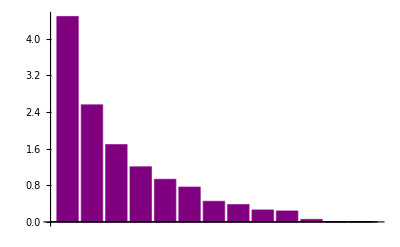

```mathematica
BarChart[varianceOfEachColumn4,ChartStyle->Purple]
```

```mathematica
cumulativeVariance3=Accumulate[varianceOfEachColumn3/Total@varianceOfEachColumn3]
```

{0.344703,0.541196,0.670955,0.763462,0.835002,0.893468,0.928053,0.957189,0.97725,0.995616,0.999775,1.,1.}

This looks  more promising in terms of a six-variable function being able to describe the variation in the data.

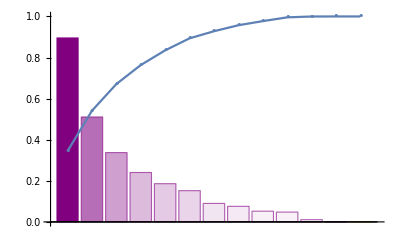

```mathematica
Show[{BarChart[1/5varianceOfEachColumn3,ColorFunction ->Function[{height},Opacity[height]],ChartStyle->Purple],ListPlot[cumulativeVariance3,Joined->True,PlotMarkers->"•"]},PlotRange->All]
```

#### Normalized

```mathematica
PCAData4=Transpose[LogNormed2]
```

(1.91145 | 1.25491 | 1.26095 | 1.23364 | 0.737543 | 0.986495 | 1.25624 | 1.3344 | 1.27274 | 1.31932 | 1.5724 | 1.20242 | 0.653926
1.40262 | 1.24516 | 1.24784 | 1.22056 | 0.725235 | 1.10975 | 1.13885 | 1.31072 | 1.30925 | 1.25624 | 1.62969 | 1.33479 | 0.936955
1.25414 | 1.22954 | 1.22688 | 1.22275 | 1.16259 | 1.09795 | 1.05962 | 1.26893 | 1.24058 | 1.23411 | 1.57945 | 1.20242 | 0.863261
1.26982 | 1.22926 | 1.2273 | 1.2224 | 1.15052 | 1.09795 | 1.0649 | 1.28743 | 1.24058 | 1.23411 | 1.68176 | 1.20242 | 0.605636
1.23822 | 1.2309 | 1.22581 | 1.22175 | 1.16259 | 1.09927 | 1.04688 | 1.25009 | 1.24303 | 1.23738 | 1.4785 | 1.20242 | 0.881631
1.41615 | 1.2496 | 1.21357 | 1.21093 | 1.17293 | 0.645591 | 1.18781 | 1.32846 | 1.29851 | 1.25357 | 1.71503 | 1.33479 | 1.00659
1.94034 | 1.25491 | 1.26121 | 1.23389 | 0.737543 | 0.986495 | 1.25881 | 1.31676 | 1.28532 | 1.33028 | 1.48367 | 1.20242 | 0.562751
1.28526 | 1.22914 | 1.22666 | 1.22265 | 1.16419 | 1.09267 | 1.06135 | 1.30559 | 1.24058 | 1.22892 | 1.77264 | 1.20242 | -0.0682083
1.3889 | 1.245 | 1.24914 | 1.2224 | 0.739987 | 0.684214 | 1.15067 | 1.29265 | 1.31306 | 1.26156 | 1.51162 | 1.33479 | 0.917389
1.3889 | 1.23996 | 1.24257 | 1.21936 | 0.816315 | 0.491268 | 1.32286 | 1.29265 | 1.32138 | 1.26156 | 1.54611 | 1.33479 | 1.06698
1.26847 | 1.23349 | 1.23069 | 1.2363 | 1.31233 | 1.35569 | 1.24883 | 1.27155 | 1.24385 | 1.24766 | 1.3633 | 1.25276 | 0.988356
1.23821 | 1.23237 | 1.22661 | 1.2227 | 1.16658 | 1.09663 | 1.0692 | 1.25009 | 1.24872 | 1.23793 | 1.49137 | 1.20242 | 0.789955
1.40262 | 1.24638 | 1.24289 | 1.21946 | 0.811782 | 0.488847 | 1.32841 | 1.31072 | 1.31685 | 1.2589 | 1.64953 | 1.33479 | 1.06224
1.22203 | 1.29233 | 1.23286 | 1.23014 | 1.19097 | 1.10714 | 1.10033 | 1.23089 | 1.25196 | 1.24172 | 1.3806 | 1.20242 | 0.809708
1.29737 | 1.24319 | 1.24372 | 1.24505 | 1.26439 | 1.2751 | 1.06641 | 1.28994 | 1.31609 | 1.28361 | 1.41707 | 1.3007 | 0.781188
1.28393 | 1.23241 | 1.22921 | 1.23409 | 1.30056 | 1.35976 | 1.25552 | 1.29 | 1.24385 | 1.24389 | 1.47591 | 1.25276 | 0.718911
1.37499 | 1.25171 | 1.24758 | 1.22439 | 0.821952 | 0.481547 | 1.35244 | 1.27426 | 1.32739 | 1.26686 | 1.41707 | 1.33479 | 1.0527
1.25228 | 1.25065 | 1.24602 | 1.25093 | 1.31783 | 1.33198 | 1.09209 | 1.25003 | 1.33038 | 1.28127 | 1.43617 | 1.25276 | 0.865576
1.28393 | 1.25065 | 1.25183 | 1.25262 | 1.26366 | 1.26622 | 1.23821 | 1.29 | 1.24385 | 1.24389 | 1.47591 | 1.25276 | 0.962461
1.25228 | 1.23241 | 1.22363 | 1.21896 | 1.15052 | 1.33198 | 1.08852 | 1.25003 | 1.33038 | 1.28127 | 1.43617 | 1.25276 | 0.852777
1.29915 | 1.23671 | 1.22868 | 1.23394 | 1.30543 | 1.35874 | 1.25925 | 1.30811 | 1.24303 | 1.24064 | 1.58645 | 1.25276 | 0.856284
1.26847 | 1.25065 | 1.25183 | 1.25247 | 1.26149 | 1.22063 | 1.24254 | 1.27155 | 1.25115 | 1.2482 | 1.37774 | 1.25276 | 0.911885
1.31284 | 1.25491 | 1.26203 | 1.25503 | 1.14971 | 1.27067 | 1.06544 | 1.31063 | 1.2414 | 1.2533 | 1.34275 | 1.3007 | 0.773612
1.28393 | 1.24744 | 1.24862 | 1.24875 | 1.2513 | 1.26511 | 1.23394 | 1.29 | 1.25034 | 1.24443 | 1.50155 | 1.25276 | 1.02154
1.3889 | 1.24532 | 1.25152 | 1.23098 | 0.885119 | 1.29694 | 1.31476 | 1.29265 | 1.32138 | 1.26156 | 1.54611 | 1.33479 | 1.14601
1.3889 | 1.24426 | 1.25514 | 1.23251 | 0.841986 | 1.29261 | 1.29734 | 1.29265 | 1.32138 | 1.26156 | 1.52408 | 1.33479 | 0.826679
1.37499 | 1.25276 | 1.25344 | 1.23197 | 0.864863 | 1.29694 | 1.32219 | 1.27426 | 1.32739 | 1.26686 | 1.41707 | 1.33479 | 1.1337
1.29737 | 1.24102 | 1.24016 | 1.23718 | 1.19408 | 1.28608 | 0.968243 | 1.28994 | 1.31609 | 1.28361 | 1.41707 | 1.3007 | 0.781188
1.3889 | 1.24209 | 1.24674 | 1.22424 | 0.836461 | 0.474194 | 1.35582 | 1.29265 | 1.32138 | 1.26156 | 1.52408 | 1.33479 | 0.792445
1.40262 | 1.24102 | 1.24132 | 1.21871 | 0.828675 | 0.483986 | 1.32502 | 1.31072 | 1.31685 | 1.2589 | 1.64076 | 1.33479 | 0.814587
1.22203 | 1.24209 | 1.23817 | 1.24554 | 1.34418 | 1.38481 | 1.19303 | 1.23089 | 1.2471 | 1.24091 | 1.38345 | 1.20242 | 0.668111
1.14 | 1.27171 | 1.27567 | 1.27313 | 1.2373 | 1.16549 | 1.09502 | 1.16515 | 1.25115 | 1.21761 | 1.51413 | 1.09342 | 0.702717
1.41615 | 1.24102 | 1.24174 | 1.21886 | 0.821952 | 0.491268 | 1.32701 | 1.32846 | 1.31306 | 1.25357 | 1.74524 | 1.33479 | 0.837438
1.35607 | 1.2496 | 1.25622 | 1.24086 | 0.994009 | 1.26845 | 1.26799 | 1.36777 | 1.28766 | 1.2597 | 1.70887 | 1.25276 | 0.423614
1.25228 | 1.24854 | 1.24262 | 1.25073 | 1.35874 | 1.26622 | 1.07412 | 1.25003 | 1.33038 | 1.28127 | 1.43617 | 1.25276 | 1.00156
1.20507 | 1.24854 | 1.24079 | 1.23758 | 1.19097 | 1.33511 | 1.1291 | 1.20846 | 1.34961 | 1.27814 | 1.45491 | 1.20242 | 0.928306
1.29915 | 1.24638 | 1.2482 | 1.24855 | 1.25276 | 1.26622 | 1.22966 | 1.30811 | 1.24953 | 1.24091 | 1.60944 | 1.25276 | 0.377608
1.40262 | 1.24102 | 1.23838 | 1.23418 | 1.17293 | 1.30448 | 1.23902 | 1.31072 | 1.31685 | 1.2589 | 1.64076 | 1.33479 | 0.848082
1.40262 | 1.24638 | 1.25328 | 1.23088 | 0.845286 | 1.28826 | 1.30049 | 1.31072 | 1.31685 | 1.2589 | 1.61849 | 1.33479 | 0.659624
1.26847 | 1.25276 | 1.25281 | 1.25267 | 1.25057 | 1.24369 | 1.24677 | 1.27155 | 1.24385 | 1.24766 | 1.3633 | 1.25276 | 1.27527
1.28393 | 1.24532 | 1.2469 | 1.24695 | 1.24763 | 1.26064 | 1.23258 | 1.29 | 1.25034 | 1.24443 | 1.48881 | 1.25276 | 0.791201
1.26847 | 1.2496 | 1.25059 | 1.25073 | 1.25203 | 1.24824 | 1.25579 | 1.27155 | 1.25115 | 1.2482 | 1.37774 | 1.25276 | 0.979111
1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276
1.25276 | 1.2581 | 1.26285 | 1.25725 | 1.17452 | 1.30983 | 1.08261 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 1.25276 | 0.917389
1.22202 | 1.25171 | 1.24867 | 1.24962 | 1.26294 | 1.31302 | 1.29383 | 1.23089 | 1.2471 | 1.24091 | 1.38345 | 1.20242 | 1.18539
1.20557 | 1.25171 | 1.24862 | 1.24957 | 1.26366 | 1.31196 | 1.29819 | 1.21131 | 1.25759 | 1.24578 | 1.27524 | 1.20242 | 1.15297)

```mathematica
Dimensions[PCAData4]
```

{46,13}

```mathematica
NewDataComponents4=PrincipalComponents[PCAData4,Method->"Correlation"];
```

```mathematica
varianceOfEachColumn4=Variance/@Transpose@NewDataComponents4
```

{4.59575,2.57381,1.62963,1.19715,0.907822,0.704277,0.460143,0.378411,0.270066,0.23032,0.0489187,0.00300062,0.000693294}

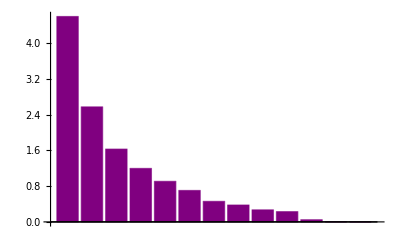

```mathematica
BarChart[varianceOfEachColumn4,ChartStyle->Purple]
```

```mathematica
cumulativeVariance4=Accumulate[varianceOfEachColumn4/Total@varianceOfEachColumn4]
```

{0.35352,0.551505,0.676861,0.76895,0.838782,0.892958,0.928353,0.957462,0.978236,0.995953,0.999716,0.999947,1.}

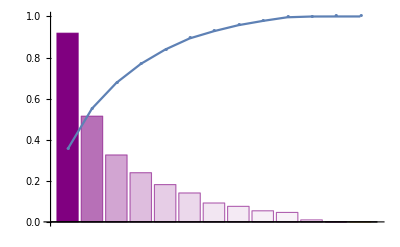

```mathematica
Show[{BarChart[1/5varianceOfEachColumn4,ColorFunction ->Function[{height},Opacity[height]],ChartStyle->Purple],ListPlot[cumulativeVariance4,Joined->True,PlotMarkers->"•"]},PlotRange->All]
```

### Correlation Matrix

```mathematica
Correlation[DatatoUse2]
```

(1. | -0.0838851 | 0.271229 | 0.258482 | 0.606635 | 0.33373 | -0.294584 | -0.526888 | -0.194399 | -0.74975 | -0.240207 | -0.120385 | 0.214991 | -0.445075
-0.0838851 | 1. | -0.555216 | 0.460072 | -0.00474525 | 0.0222463 | 0.0570004 | -0.279507 | -0.0262394 | 0.0985546 | -0.353896 | -0.165832 | 0.179423 | -0.264673
0.271229 | -0.555216 | 1. | -0.633469 | 0.25258 | -0.0991034 | -0.269334 | 0.0429598 | -0.0484502 | -0.239614 | 0.29755 | 0.0103618 | -0.0981184 | 0.37217
0.258482 | 0.460072 | -0.633469 | 1. | 0.588676 | 0.605684 | -0.120574 | -0.430435 | -0.383033 | -0.126844 | -0.5825 | -0.448233 | 0.12625 | -0.577815
0.606635 | -0.00474525 | 0.25258 | 0.588676 | 1. | 0.653866 | -0.432335 | -0.493919 | -0.52948 | -0.408954 | -0.417618 | -0.550087 | 0.0556044 | -0.333557
0.33373 | 0.0222463 | -0.0991034 | 0.605684 | 0.653866 | 1. | -0.307771 | -0.325735 | -0.309641 | -0.110675 | -0.44131 | -0.395825 | -0.00780498 | -0.352955
-0.294584 | 0.0570004 | -0.269334 | -0.120574 | -0.432335 | -0.307771 | 1. | 0.313594 | 0.201145 | 0.0827052 | 0.114213 | 0.444218 | 0.328539 | -0.259118
-0.526888 | -0.279507 | 0.0429598 | -0.430435 | -0.493919 | -0.325735 | 0.313594 | 1. | 0.164145 | 0.290585 | 0.630205 | 0.570061 | -0.31892 | 0.342209
-0.194399 | -0.0262394 | -0.0484502 | -0.383033 | -0.52948 | -0.309641 | 0.201145 | 0.164145 | 1. | 0.578043 | 0.190174 | 0.635146 | 0.130825 | -0.0293615
-0.74975 | 0.0985546 | -0.239614 | -0.126844 | -0.408954 | -0.110675 | 0.0827052 | 0.290585 | 0.578043 | 1. | -0.0841716 | 0.219864 | -0.032633 | 0.199581
-0.240207 | -0.353896 | 0.29755 | -0.5825 | -0.417618 | -0.44131 | 0.114213 | 0.630205 | 0.190174 | -0.0841716 | 1. | 0.243731 | -0.498631 | 0.412785
-0.120385 | -0.165832 | 0.0103618 | -0.448233 | -0.550087 | -0.395825 | 0.444218 | 0.570061 | 0.635146 | 0.219864 | 0.243731 | 1. | 0.244028 | -0.0169938
0.214991 | 0.179423 | -0.0981184 | 0.12625 | 0.0556044 | -0.00780498 | 0.328539 | -0.31892 | 0.130825 | -0.032633 | -0.498631 | 0.244028 | 1. | -0.324742
-0.445075 | -0.264673 | 0.37217 | -0.577815 | -0.333557 | -0.352955 | -0.259118 | 0.342209 | -0.0293615 | 0.199581 | 0.412785 | -0.0169938 | -0.324742 | 1.)

No |Pearson’s correlation coefficients| above 0.8 --> can continue. Thirteen variables, subsets of 6 --> there should be 13C6 = 1716 combinations.

```mathematica
framed[n_]:=If[n>0.8,Framed[n],n]
```

```mathematica
SetAttributes[framed,Listable]
```

```mathematica
framed[Correlation[DatatoUse2]]
```

(1. | -0.0838851 | 0.271229 | 0.258482 | 0.606635 | 0.33373 | -0.294584 | -0.526888 | -0.194399 | -0.74975 | -0.240207 | -0.120385 | 0.214991 | -0.445075
-0.0838851 | 1. | -0.555216 | 0.460072 | -0.00474525 | 0.0222463 | 0.0570004 | -0.279507 | -0.0262394 | 0.0985546 | -0.353896 | -0.165832 | 0.179423 | -0.264673
0.271229 | -0.555216 | 1. | -0.633469 | 0.25258 | -0.0991034 | -0.269334 | 0.0429598 | -0.0484502 | -0.239614 | 0.29755 | 0.0103618 | -0.0981184 | 0.37217
0.258482 | 0.460072 | -0.633469 | 1. | 0.588676 | 0.605684 | -0.120574 | -0.430435 | -0.383033 | -0.126844 | -0.5825 | -0.448233 | 0.12625 | -0.577815
0.606635 | -0.00474525 | 0.25258 | 0.588676 | 1. | 0.653866 | -0.432335 | -0.493919 | -0.52948 | -0.408954 | -0.417618 | -0.550087 | 0.0556044 | -0.333557
0.33373 | 0.0222463 | -0.0991034 | 0.605684 | 0.653866 | 1. | -0.307771 | -0.325735 | -0.309641 | -0.110675 | -0.44131 | -0.395825 | -0.00780498 | -0.352955
-0.294584 | 0.0570004 | -0.269334 | -0.120574 | -0.432335 | -0.307771 | 1. | 0.313594 | 0.201145 | 0.0827052 | 0.114213 | 0.444218 | 0.328539 | -0.259118
-0.526888 | -0.279507 | 0.0429598 | -0.430435 | -0.493919 | -0.325735 | 0.313594 | 1. | 0.164145 | 0.290585 | 0.630205 | 0.570061 | -0.31892 | 0.342209
-0.194399 | -0.0262394 | -0.0484502 | -0.383033 | -0.52948 | -0.309641 | 0.201145 | 0.164145 | 1. | 0.578043 | 0.190174 | 0.635146 | 0.130825 | -0.0293615
-0.74975 | 0.0985546 | -0.239614 | -0.126844 | -0.408954 | -0.110675 | 0.0827052 | 0.290585 | 0.578043 | 1. | -0.0841716 | 0.219864 | -0.032633 | 0.199581
-0.240207 | -0.353896 | 0.29755 | -0.5825 | -0.417618 | -0.44131 | 0.114213 | 0.630205 | 0.190174 | -0.0841716 | 1. | 0.243731 | -0.498631 | 0.412785
-0.120385 | -0.165832 | 0.0103618 | -0.448233 | -0.550087 | -0.395825 | 0.444218 | 0.570061 | 0.635146 | 0.219864 | 0.243731 | 1. | 0.244028 | -0.0169938
0.214991 | 0.179423 | -0.0981184 | 0.12625 | 0.0556044 | -0.00780498 | 0.328539 | -0.31892 | 0.130825 | -0.032633 | -0.498631 | 0.244028 | 1. | -0.324742
-0.445075 | -0.264673 | 0.37217 | -0.577815 | -0.333557 | -0.352955 | -0.259118 | 0.342209 | -0.0293615 | 0.199581 | 0.412785 | -0.0169938 | -0.324742 | 1.)

### “Backwards” Linear Regression

```mathematica
whichParameters2New=Subsets[Range[Length@First@DatatoUse2-1],{6}];
```

```mathematica
Length[whichParameters2New=Subsets[Range[Length@First@DatatoUse2-1],{6}]]
```

1716

```mathematica
whichParameters2New2=Append[#,-1]&/@whichParameters2New;
```

```mathematica
Length[whichParameters2New2]
```

1716

```mathematica
test12=whichParameters2New2[[1]]
```

{1,2,3,4,5,6,-1}

```mathematica
test22=Part[DatatoUse2,All,test1];
```

```mathematica
Length[test22]
```

46

```mathematica
LinearModelFit[test22,Table[x[i],{i,1,6}],Table[x[i],{i,1,6}]]["RSquared"]
```

0.489373

```mathematica
allRSquared2=MapIndexed[
Function[
{parameters,index},
regressThese=Part[DatatoUse2,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,6}],Table[x[i],{i,1,6}]]["RSquared"]
],
whichParameters2New2
];
```

```mathematica
Length[allRSquared2]
```

1716

```mathematica
bestFits=TakeLargestBy[allRSquared2,Last,UpTo[5]]
```

{573→0.685917,391→0.685897,447→0.685832,644→0.685761,181→0.685036}

```mathematica
whichParameters2New2[[573]]
```

{1,4,5,7,10,13,-1}

```mathematica
TableForm[Part[whichParameters2New2,{573,391,447,644,181}]]
```

1 | 4 | 5 | 7 | 10 | 13 | -1
1 | 3 | 4 | 7 | 10 | 13 | -1
1 | 3 | 5 | 7 | 10 | 13 | -1
1 | 4 | 7 | 9 | 10 | 13 | -1
1 | 2 | 4 | 7 | 10 | 13 | -1

Reminder: List of variables is {ET,IP,EHOMO,η,ELUMO,Qp,DM,MW,γ,D,cLogP,TPSA,Druglikeness,logMU}
1=Etotal, 2=Ionization potential, 3=Ehomo, 4=absolute hardness, 5=Elumo, 6=an apparently-useless charge descriptor, 7=dipole moment calculated by DFT, 9=surface tension(of all things!!), 10=density, 13= “Druglikeness” score (hilarious because it’s loosely inversely correlated with potency for this series).

Conclusion: I tested a matrix of 7 DFT descriptors and six physicochemical descriptors for the best combination of six variables to explain the data. Four of the five top models used 4 DFT descriptors and 2 physicochemical descriptors, so clearly DFT data enhanced the models. Ehomo and absolute hardness being so prevalent got me thinking about how you can apply FMO theory to drug:protein interactions. Still none of the models had a great R^2; the best had R^2=0.685917, --> R=0.8282. But it should not be easy chemically/quantitatively predict a phenotypic outcome like effective dose, so I’m still encouraged. I’d be curious to see what happens when I can do my own DFT calculations and take a FMO Theory approach, seeing if frontier orbital coefficients predict activity, and doing traditional “SAR” with a target-engagement based assay. I hypothesize that 1) Higher-correlation models will emerge and 2) Those models will still benefit from DFT.

### Trying a Non-linear Regression

```mathematica
nonlinearinput1=DatatoUse2[[All,{1,4,5,7,10,13,-1}]];
```

```mathematica
nonlinear6=NonlinearModelFit[
nonlinearinput1,
a+b x1+c x2+d x3+e x4+f x5+q x6+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2+r x6^2,{a,b,c,d,e,f,g,h,n,m,k,q,r},
{x1,x2,x3,x4,x5,x6}
]
```

FittedModel[28.1918-0.0000946278 x1-7.67461×10^-10 («2»)^2+«13»+0.0390206 x6-0.0118394 x6^2]

```mathematica
nonlinear6["RSquared"]
```

0.915859

Sweet! Now we’re moving toward an actually useful model. I wonder if you can do a “backwards” non-linear regression and get the same result?

```mathematica
allRSquaredNonlinear=MapIndexed[
Function[
{parameters,index},
regressThese=Part[DatatoUse2,All,parameters];
First@index->NonlinearModelFit[regressThese,a+b x1+c x2+d x3+e x4+f x5+q x6+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2+r x6^2,{a,b,c,d,e,f,g,h,n,m,k,q,r},
{x1,x2,x3,x4,x5,x6}]["RSquared"]
],
whichParameters2New2
];
```

```mathematica
(*Well, it ran without crashing, that's a start...*)
```

```mathematica
Length[allRSquaredNonlinear]
```

1716

```mathematica
bestFitsNonLinear=TakeLargestBy[allRSquaredNonlinear,Last,UpTo[5]]
```

{442→0.944406,1442→0.943539,1426→0.943429,1423→0.942312,1549→0.941973}

```mathematica
TableForm[Part[whichParameters2New2,{442,1442,1426,1423,1549}]]
```

1 | 3 | 5 | 7 | 9 | 11 | -1
3 | 5 | 8 | 10 | 11 | 12 | -1
3 | 5 | 7 | 9 | 10 | 11 | -1
3 | 5 | 7 | 8 | 11 | 12 | -1
4 | 5 | 7 | 8 | 11 | 12 | -1

*Cue Uncle Fester in 1960’s Addams Family* “Veeery Iiinteresting!”
The ones with 3, 5, and 7: this is literally FMO Theory - Ehomo, Elumo, dipole moment. 1 is Etotal, 4 is absolute hardness. On the non-DFT side: 8 is Molecular Weight, 9 is surface tension, 10 is density, 11 is cLogP - of course that shows up! - and 12 is Total Polar Surface Area... OK Lepinski you win.

```mathematica
BestModelToTest=DatatoUse2[[All,{1,3,5,7,9,11,-1}]];
```

```mathematica
{training1,testing1}=TakeDrop[RandomSample[BestModelToTest],35];
```

```mathematica
Dimensions[testing1]
```

{11,7}

```mathematica
Dimensions[training1]
```

{35,7}

```mathematica
nonlinear6and35 = NonlinearModelFit[
training1,a+b x1+c x2+d x3+e x4+f x5+q x6+g x1^2+h x2^2+n x3^2+m x4^2+k x5^2+r x6^2,{a,b,c,d,e,f,g,h,n,m,k,q,r},
{x1,x2,x3,x4,x5,x6}]
```

FittedModel[«16»+1.08539 x6-0.340019 x6^2]

```mathematica
nonlinear6and35["RSquared"]
```

0.961894

```mathematica
observed1=testing1[[All,-1]]
```

{0.03,1.,0.86,0.23,-0.03,1.33,1.66,0.38,0.76,0.58,1.68}

```mathematica
predicted1=Map[
nonlinear6and35["BestFit"]/.Thread[{x1,x2,x3,x4,x5,x6,output}->#]&,
testing1
]
```

{0.427485,0.488219,2.08325,0.728537,1.02194,1.0362,1.89991,0.742458,1.41332,0.675525,1.69712}

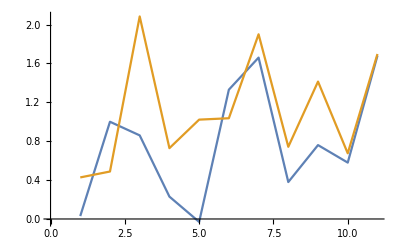

```mathematica
ListLinePlot[{observed1,predicted1}]
```

So, the best model makes a decent prediction about half the time. I note that they at least moved in the same direction 9 times out of 11.

```mathematica
combined1=Transpose[{predicted1,observed1}]
```

{{0.427485,0.03},{0.488219,1.},{2.08325,0.86},{0.728537,0.23},{1.02194,-0.03},{1.0362,1.33},{1.89991,1.66},{0.742458,0.38},{1.41332,0.76},{0.675525,0.58},{1.69712,1.68}}

```mathematica
Correlation[combined1]
```

{{1.,0.613015},{0.613015,1.}}

That’s actually crappy.